# Geometric groups

Evaluate this stuffƒ

### basic operations

```mathematica
Off[General::"spell1"]
```

Here is a handy method of building groups and other kinds of lists of useful things

```mathematica
a_⊙b_:=Join @@ Outer[Dot,a,b,1]    (*generates all dot products of elts of a,b*)
x_⊙y_⊙z_:=x⊙(y⊙z)
```

```mathematica
f_⊗g_:=(f⊙{#})& /@ g;                          (*applies g to object f*)

f_⋆A_:=Map[f,A,{2}];                          


f_⊕v_:=Map[#+v&,f,{2}]


Subscript[A_, n_]:=Table[MatrixPower[A,k],{k,0,n-1}]
```

```mathematica
A_⋄B_:=Inverse[B].A.B

A_⋄B_⋄C_:=(A⋄B)⋄C
```

### specific transforms

```mathematica
rot[t_]:=({{Cos[t], Sin[t], 0}, {-Sin[t], Cos[t], 0}, {0, 0, 1}})
trans[{x_,y_}]:=({{1, 0, 0}, {0, 1, 0}, {x, y, 1}})
refx=({{-1, 0, 0}, {0, 1, 0}, {0, 0, 1}});

ident=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
scale[s_]:=scale[s]=({{s, 0, 0}, {0, s, 0}, {0, 0, 1}})
scale[{sx_,sy_}]:=({{sx, 0, 0}, {0, sy, 0}, {0, 0, 1}});
refy=rot[-Pi/2].refx.rot[Pi/2];
```

```mathematica
r3=	Subscript[(rot[2π/3]), 3];
r6 =Subscript[(rot[2π/6]), 6];
```

### moving among models:

```mathematica
homo2cart[vect_]:=Drop[vect,-1]/vect⟦-1⟧

cart2homo[vect_]:=Append[vect,1]

stereo[vect_]:=Drop[vect,-1]/(-vect[[-1]]+1)
stereo2sphere[vect_]:=If[vect.vect>1,
		Append[#,Sqrt[1-#.#]]&[2vect/(vect.vect+1)],
		Append[#,-Sqrt[1-#.#]]&[2vect/(vect.vect+1)]]

Flatproj[vect_]:=Drop[vect,-1]
```

```mathematica
SuperPlus[v_]:=cart2homo[v];
SubPlus[v_]:=homo2cart[v];
```

### helpful graphics stuff

#### miscellaneous

```mathematica
spline[x0_,x1_,v0_,v1_]:=
	a t^3+b t^2 + c t + d/.
		{a->-v1+v0-2x1+2x0,
			b->3x1-3x0-2v0+v1,
			c->v0,d->x0}
```

```mathematica
‖v_‖:=√(v.v)
```

```mathematica
OverBar[v_]:=v/‖v‖//N
```

#### spherical polygon routines

abovelist returns f applied to the components (of length >2) of poly that lie in the positive view direction.  That is, we check which points of poly have poly.view >0.
view can be seen as an axis of projection (say for spherical plots) or as a sided homogeneous line (for poly in homo coords).

```mathematica
abovelist[poly_,view_,f_]:=
	Module[{i,current,dp,pp},
		i=1;
		current={};
		dp=#.view&/@ poly;
	Which[
		And @@ (# <0 & /@ dp), {},
		And @@ (# >0 & /@ dp) && Length[poly]>2,{f[poly]},
		And @@ (# >0 & /@ dp) && Length[poly]<3,{},
     dp⟦1⟧>0,abovelist[RotateLeft[poly],view,f],
			True,
While[dp⟦i⟧<=0, i++];pp=f[poly];
While[dp⟦i⟧>=0 && i< Length[poly],
			current=Append[current,pp⟦i⟧];i++];
Which[
			i==Length[poly] && dp⟦i⟧>=0 && Length[current]>1,{Append[current,pp⟦i⟧]},
			i==Length[poly] && Length[current]>2,{current},
			i==Length[poly], Return[{}],
			Length[current]>2,
			        Append[abovelist[Drop[poly,i],view,f],current],
			True,abovelist[Drop[poly,i-1],view,f]]]];
```

```mathematica
re2co[v_]:=v⟦1⟧+I v⟦2⟧
```

```mathematica
fillin[v1_,v2_,res_]:=Module[{},
		t1=Arg[re2co[v1]];
		t2=Arg[re2co[v2]];
		nn=Abs[t1-t2];
		Which[
			nn>Pi &&t1<t2, t1=t1+2Pi,
			nn>Pi  &&t1>t2, t2=t2+2Pi];
		nnn=Abs[Ceiling[(t1-t2)/res]];
		Which[nnn==0,{},True,
		nnnn=(t2-t1)/nnn;
		
		Table[{Cos[t1+nnnn k],Sin[t1+nnnn k]}//N,{k,1,nnn-1}]//N]]
```

OverBar[-{a,b,c}],	OverBar[-{-b,a,0}]  for back

```mathematica
FlatSpherePoly[poly_,view_,bi_,res_]:=
	Join[#,fillin[#⟦-1⟧,#⟦1⟧,res]]& /@ abovelist[poly,view,#.Transpose[{bi,view×bi}]&]
```

```mathematica
st[a_,b_,c_]:=Show[Graphics[Join[
		
			Join @@
					({Hue[.1],Polygon[#]}&/@
							(Join @@ (FlatSpherePoly[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}],.1]&/@ 
										ppp
									))
					),	
				
				{GrayLevel[.5],Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/50}]]}
			
			
			
			],AspectRatio->Automatic,Axes->False,PlotRange->All]]
```

```mathematica
FlatSphereCurve[curve_,view_,bi_]:=
	 abovelist[curve,view,#.Transpose[{bi,view×bi}]&]
```

#### homoline stuff

```mathematica
sform[{a_,0,0}]:={1,0,0};
sform[{a_,b_,0}]:={a/b,1,0};
sform[{a_,b_,c_}]:={a/c,b/c,1};
```

(*to take pt transform to line transform*)

```mathematica
SuperDagger[M_]:=Transpose[Inverse[M]]
```

this takes a homoline to the point closest to the origin on the line

```mathematica
SuperStar[{a_,b_,c_}]:={-c a/(a^2+b^2),-c b/(a^2+b^2),1}
```

Calculates the distance from a hline to a hpt

```mathematica
dist2line[hline_,hpt_]:=
	‖hpt.(trans[Drop[SuperStar[hline],-1]])‖
```

And this gives a point closest from hline to hpt

```mathematica
closestpt[hline_,hpt_]:=SuperStar[(hline.Transpose[#])].#&[
		trans[homo2cart[hpt]]]
```

This gives a signed distance; assuming the normal is not normalized. Note what happens if hpt⟦3⟧==0!

```mathematica
signeddist[hline_,hpt_]:=hline.hpt/‖Drop[hline,-1]‖/hpt⟦3⟧
```

In homoline[pt1,pt2], a choice of normal is given by {a,b} (note not scaled!); this normal points left if one is walking from pt1 to pt2.
Also, homoline[x1,x2] has third coord pos iff x1 to x2 clockwise about origin

```mathematica
homoline[{a_,b_},{c_,d_}]:={b-d,-a+c,-b c+a d}
```

```mathematica
homolines[poly_]:= 
	Module[{},
		pp=Append[poly,poly⟦1⟧];
		Table[homoline[pp⟦i⟧,pp⟦i+1⟧],{i,1,Length[poly]}]]
```

```mathematica
dist2line[hline_,hpt_]:=
	‖hpt.(trans[Drop[SuperStar[hline],-1]])‖
```

```mathematica
inhomopoly[homopoly_,homopt_]:=And @@ (
	#>0& /@ (#.homopt& /@ homopoly))
```

```mathematica
drawhomoline[{a_,b_,c_}]:=
	Module[{p,v},
		v={-b,a}/√(a^2+b^2);
		p=-c {a,b}/(a^2+b^2);
		Line[{p+300 v,p-300 v}]]
```

## the wallpaper groups

### Setting up the groups

The names of the wallpaper groups are given in wallpapergps
atr is the "type" of the group: Z is shearable, Y is stretchable, X is only orthogonally transformable.

G is enough of the group to tile a tile
t is gives the side of the tile
fund gives a polygonal fundamental domain
mirlines gives one copy of each mirror line
rotpts gives the rotation pts.   At the moment it is not clear if the dihedral pts need to be included.
S gives a nice matrix to "set the group up"

H gives the subgroup G/D4
outfund  is a list of lines bounding the output fund region in math coords
tout are the max x-y dimensions of the outfund.

```mathematica
wallpapergps={"2222","22*","22x","2*22","*2222","o","xx","x*","**","442","4*2","*442","333","3*3","*333","632","*632"};
```

```mathematica
(Subscript[mirlines, #]={} )&/@ wallpapergps;
(rotpts[2][#]={})& /@ wallpapergps;
(rotpts[3][#]={})& /@ wallpapergps;
(rotpts[4][#]={})& /@ wallpapergps;
(rotpts[6][#]={})& /@ wallpapergps;
```

```mathematica
(Subscript[atr, #]=Z)&/@{"2222","o"};
(Subscript[atr, #]=Y)&/@{"22*","22x","2*22","*2222","xx","x*","**"};
(Subscript[atr, #]=X)&/@{"442","4*2","*442","333","3*3","*333","632","*632"};
```

```mathematica
(Subscript[c, #]="do")&/@ wallpapergps;
```

```mathematica
Subscript[G, "2222"]={ident, rot[Pi]⋄trans[{1,1}]};

Subscript[t, "2222"]={{2,0},{0,2}};
Subscript[fund, "2222"]={{0,0},{2,0},{2,1},{0,1}};

rotpts[2]["2222"]={{0,0},{1,0},{1,1},{0,1}};
```

```mathematica
Subscript[G, "22*"]={ident,trans[-{1,1}].rot[Pi].trans[{1,1}]}⊙{ident,trans[-{2,0}].refx.trans[{2,0}]};

Subscript[t, "22*"]={{4,0},{0,2}};
Subscript[fund, "22*"]={{0,0},{2,0},{2,1},{0,1}};

rotpts[2]["22*"]={{1,0},{1,1}};
Subscript[mirlines, "22*"]={homoline[{2,0},{2,1}]};

rotpts[2]["22*"]={{1,0},{1,1},{3,0},{3,1}};
Subscript[mirlines, "22*"]={homoline[{2,0},{2,1}],homoline[{0,0},{0,1}]};
```

```mathematica
Subscript[G, "22x"]={ident,rot[Pi].trans[{4,2}],trans[-{1,0}].refx.trans[{1,1}],rot[Pi].trans[-{1,0}].refx.trans[{1,1}]};

Subscript[t, "22x"]=Subscript[t, "22*"];
Subscript[fund, "22x"]=Subscript[fund, "2222"];

rotpts[2]["22x"]={{1,0},{1,1}};
rotpts[2]["22x"]={{1,0},{1,1},{3,0},{3,1}};
```

```mathematica
Subscript[G, "2*22"]={ident,rot[Pi]⋄trans[{1,1}]}⊙{ident,refx⋄trans[{2,0}]}⊙{ident,refy⋄trans[{0,2}]};

Subscript[t, "2*22"]={{4,0},{0,4}};
Subscript[fund, "2*22"]=Subscript[fund, "2222"];
Subscript[mirlines, "2*22"]={homoline[{0,0},{2,0}],homoline[{0,0},{0,2}]};

rotpts[2]["2*22"]={{1,1}};
rotpts[2]["2*22"]={{1,1},{3,1},{1,3},{3,3}};
Subscript[mirlines, "2*22"]={homoline[{0,0},{2,0}],homoline[{0,0},{0,2}],homoline[{2,2},{2,0}],homoline[{2,2},{0,2}]};
```

```mathematica
(*alternatively*)
```

```mathematica
Subscript[G, "2*22"]={ident,(refx⋄rot[-Pi/4])}
			⊙
	{ident,(refx⋄rot[Pi/4])⋄trans[{2,0}]};

Subscript[t, "2*22"]={{2,0},{0,2}};
Subscript[tout, "2*22"]={{2,0},{0,1}};
Subscript[fund, "2*22"]={{0,0},{2,0},{1,1}};
Subscript[mirlines, "2*22"]={homoline[{0,0},{2,2}],homoline[{2,0},{0,2}]};
rotpts[2]["2*22"]={{1,0},{0,1}};
```

```mathematica
Subscript[G, "*2222"]={ident,refx⋄trans[{1,0}]}⊙{ident,refy⋄trans[{0,1}]};
Subscript[t, "*2222"]={{2,0},{0,2}};

Subscript[fund, "*2222"]={{0,0},{1,0},{1,1},{0,1}};
Subscript[mirlines, "*2222"]=homolines[{{0,0},{1,0},{1,1},{0,1}}];
```

```mathematica
Subscript[G, "o"]={ident};
Subscript[t, "o"]={{1,0},{0,1}};
Subscript[fund, "o"]={{0,0},{1,0},{1,1},{0,1}};
```

```mathematica
Subscript[G, "xx"]={ident,refx.trans[{1,1}]};
Subscript[t, "xx"]={{1,0},{0,2}};
Subscript[fund, "xx"]={{0,0},{1,0},{1,1},{0,1}};
```

```mathematica
Subscript[G, "x*"]=Subscript[G, "xx"]⊙{ident,refx⋄trans[{1,0}]};
Subscript[t, "x*"]={{2,0},{0,2}};
Subscript[fund, "x*"]={{0,0},{1,0},{1,1},{0,1}};
Subscript[mirlines, "x*"]={homoline[{1,0},{1,1}]};
```

```mathematica
Subscript[G, "**"]={ident,refx.trans[{2,0}]};
Subscript[t, "**"]={{2,0},{0,1}};
Subscript[fund, "**"]={{0,0},{1,0},{1,1},{0,1}};
Subscript[mirlines, "**"]={homoline[{1,0},{1,1}],homoline[{0,1},{0,0}]};
```

```mathematica
Subscript[G, "442"]=Subscript[(rot[Pi/2]⋄trans[{1,1}]), 4];
Subscript[t, "442"]={{2,0},{0,2}};
Subscript[fund, "442"]={{0,0},{1,0},{1,1},{0,1}};
rotpts[4]["442"]={{0,0},{1,1}};
rotpts[2]["442"]={{1,0}};
rotpts[2]["442"]={{1,0},{0,1}};
```

```mathematica
Subscript[G, "4*2"]=trans[-{1,1}].#.trans[{1,1}] & /@ Subscript[(rot[Pi/2]), 4]⊙
		{ident,refx⋄trans[{2,0}]}⊙
		{ident,refy⋄trans[{0,2}]};
Subscript[t, "4*2"]={{4,0},{0,4}};
Subscript[fund, "4*2"]={{0,0},{1,0},{1,1},{0,1}};
Subscript[mirlines, "4*2"]={homoline[{0,0},{1,0}]};
rotpts[4]["4*2"]={{1,1}};
rotpts[4]["4*2"]={{1,1},{3,1},{1,3},{3,3}};
Subscript[mirlines, "4*2"]={homoline[{0,0},{2,0}],homoline[{0,0},{0,2}],homoline[{2,2},{2,0}],homoline[{2,2},{0,2}]};
```

```mathematica
(*alternatively*)
```

```mathematica
Subscript[G, "4*2"]={ident,rot[-Pi/2]⋄trans[{1,0}]}⊙
		{ident,(refx⋄rot[-Pi/4])}
			⊙
	{ident,(refx⋄rot[Pi/4])⋄trans[{2,0}]};
Subscript[t, "4*2"]={{2,0},{0,2}};
Subscript[tout, "4*2"]={{2,0},{0,1}};
Subscript[fund, "4*2"]={{0,0},{1,1},{0,1}};
rotpts[4]["4*2"]={{1,0},{0,1}};
Subscript[mirlines, "4*2"]={homoline[{0,0},{2,2}],homoline[{2,0},{0,2}]};
```

```mathematica
Subscript[G, "*442"]={refx⋄rot[-Pi/4],ident}⊙Subscript[(rot[Pi/2]⋄trans[{1,1}]), 4];
Subscript[t, "*442"]={{2,0},{0,2}};
Subscript[tout, "*442"]={{1,0},{0,1}};
Subscript[fund, "*442"]={{0,0},{1,0},{1,1}};
Subscript[mirlines, "*442"]=Join[homolines[Subscript[fund, "*442"]],homolines[{{0,2},{1,1},{0,1}}]];
```

```mathematica
Subscript[G, "333"]=
	(i=0;tt={{3/2,√3/2},{3/2,-√3/2},{3/2,-√3/2}};	Join @@({#,#.trans[tt⟦++i⟧]}&/@
	Subscript[(rot[2Pi/3]⋄trans[{1/2,√3/2}]), 3]));

Subscript[H, "333"]=Subscript[(rot[2Pi/3]⋄trans[{1/2,√3/2}]), 3];
Subscript[outfund, "333"]={{0,0},{3/2,0},{3/2,√3},{0,√3}};

Subscript[tout, "333"]={{3/2,0},{0,√3}};
			
Subscript[t, "333"]={{3,0},{0,√3}};
Subscript[fund, "333"]={{0,0},{1,0},{3/2,√3/2},{1/2,√3/2}};

rotpts[3]["333"]={{0,0},{1,0},{1/2,√3/2}};

rotpts[3]["333"]={{-1/2,(√3)/2},{0,0},{1/2,(√3)/2},{1,0},{3/2,(√3)/2},{2,0},{5/2,(√3)/2}};
```

```mathematica
Subscript[G, "3*3"]=
		
	(Append[Drop[#,{2}],#⟦2⟧.trans[{-√3,0}]]&[
	(Subscript[(rot[2Pi/3]⋄trans[{√3/2,1/2}]), 3]⊙({ident,refy⋄rot[-Pi/3]⋄trans[{√3,0}]}))])⊙{ident,refy⋄trans[{0,3/2}]};
					
					
		
Subscript[H, "3*3"]=Subscript[(rot[2Pi/3]⋄trans[{√3/2,1/2}]), 3];
Subscript[outfund, "3*3"]={{0,0},{√3,0},{√3/2,3/2}};
	
Subscript[t, "3*3"]={{√3,0},{0,3}};
Subscript[tout, "3*3"]={{√3,0},{0,3/2}};
Subscript[fund, "3*3"]={{0,0},{√3,0},{√3/2,1/2}};
Subscript[mirlines, "3*3"]={homoline[{0,0},{√3,0}]};
rotpts[3]["3*3"]={{√3/2,1/2}};

rotpts[3]["3*3"]={{0,1},{0,2},{(√3)/2,1/2},{(√3)/2,5/2}};
Subscript[mirlines, "3*3"]=Join[homolines[{{0,0},{√3,0},{√3/2,3/2}}],{homoline[{0,3/2},{√3,3/2}]}];
```

```mathematica
Subscript[G, "*333"]=	(i=0;ttt={{3/2,√3/2},{3/2,-√3/2},{0,0}};tt=ttt⟦#⟧&/@{1,2,2,1,2,1};
		Join @@ 
			({#,#.trans[tt⟦++i⟧]}&/@(
		{ident,refy⋄rot[-Pi/3]⋄trans[{1,0}]}⊙Subscript[(rot[2Pi/3]⋄trans[{1/2,√3/2}]), 3])));
Subscript[H, "*333"]=
		{ident,refy⋄rot[-Pi/3]⋄trans[{1,0}],rot[-2Pi/3]⋄trans[{1,0}]};
Subscript[t, "*333"]={{3,0},{0,√3}};
Subscript[tout, "*333"]={{2,0},{0,√3/2}};

Subscript[fund, "*333"]={{0,0},{1,0},{1/2,√3/2}};
Subscript[outfund, "*333"]={{0,0},{2,0},{3/2,√3/2},{1/2,√3/2}};
Subscript[mirlines, "*333"]=homolines[Subscript[fund, "*333"]];

Subscript[mirlines, "*333"]=Join[homolines[Subscript[fund, "*333"]],homolines[#+{3/2,√3/2}&/@ Subscript[fund, "*333"]],
	{homoline[{1,√3},{2,0}],homoline[{2,0},{3,√3}]}];
```

```mathematica
Subscript[G, "632"]=	(i=0;ttt={{3/2,√3/2},{3/2,-√3/2}};tt=ttt⟦#⟧&/@{1,2,2,1,2,1};
		Join @@ 
			({#,#.trans[tt⟦++i⟧]}&/@
					
			(Subscript[(rot[Pi]⋄trans[{3/4,√3/4}]), 2]⊙Subscript[(rot[2Pi/3]⋄trans[{1/2,√3/2}]), 3])));
			
			
Subscript[H, "632"]={ident,rot[Pi]⋄trans[{3/4,√3/4}],rot[-2Pi/3]⋄trans[{1,0}]};

Subscript[tout, "632"]={{1,0},{0,√3}};
		

Subscript[t, "632"]={{3,0},{0,√3}};
Subscript[fund, "632"]={{0,0},{1,0},{1/2,√3/2}};

Subscript[outfund, "632"]={{0,0},{2,0},{3/2,√3/2},{1/2,√3/2}};
rotpts[6]["632"]={{0,0}};
rotpts[3]["632"]={{1/2,√3/2}};
rotpts[2]["632"]={{3/4,√3/4}};

rotpts[2]["632"]=Drop[homo2cart/@(({3/4,(√3)/4,1}.#&/@ Subscript[G, "632"])//Union),{-3}];
rotpts[6]["632"]={{0,0},{3/2,√3/2}};

rotpts[3]["632"]={{-1/2,(√3)/2},{1/2,(√3)/2},{1,0},{2,0},{5/2,(√3)/2}};
```

```mathematica
Subscript[G, "*632"]={ident,rot[Pi/3],refy⋄rot[Pi/6]}⊙({ident,rot[Pi]⋄trans[{3/4,√3/4}]}⊙{ident,refx⋄trans[{3/2,0}]}⊙{ident,refy⋄trans[{0,√3/2}]});
	
	Subscript[H, "*632"]={ident,refy⋄rot[Pi/6],refy⋄rot[Pi/3]};
	
Subscript[t, "*632"]=Subscript[t, "632"];

Subscript[tout, "*632"]=Subscript[tout, "632"];

Subscript[fund, "*632"]={{0,0},{1,0},{3/4,√3/4}};

Subscript[outfund, "*632"]={{0,0},{1,0},{1/2,√3/2},{0,√3/2}};
Subscript[mirlines, "*632"]=homolines[Subscript[fund, "*632"]];

Subscript[mirlines, "*632"]=Drop[Drop[(sform/@(homolines[Subscript[fund, "*632"]]⊙(SuperDagger[#]&/@ Subscript[G, "632"])))//Union,{12}],{10}];
```

```mathematica
(Subscript[S, #]=(ss=#;
	trans[-Plus @@ #/Length[#]&[Subscript[fund, ss]]].{{#,0,0},{0,#,0},{0,0,1}}&[1/Max[#⟦1⟧ &/@ Subscript[fund, #]]/2].trans[{.5,.5}]))&/@  wallpapergps;
```

```mathematica
(Subscript[hpoly, #]=homolines[Subscript[fund, #]])& /@ wallpapergps;
```

```mathematica
(Subscript[mirlines, #]=sform/@Subscript[mirlines, #])&/@wallpapergps;
```

```mathematica
(Subscript[fundims, #]={Max[#⟦1⟧&/@(Subscript[fund, #])],
			Max[#⟦2⟧&/@(Subscript[fund, #])]})&/@ wallpapergps;
```

#### For a number of groups we can derive H, K and outfund immediately:

```mathematica
(Subscript[H, #]={ident};  Subscript[outfund, #]=Subscript[fund, #])&/@{"2222", "22*","22x","*2222","o","**","x*","xx","442","2*22","4*2","*442"};
```

```mathematica
(Subscript[tout, #]=Subscript[t, #])&/@{"2222","22*","22x","*2222","442","o","x*","**","xx"};
```

#### But others take more care and are dealt with above.

### quick illustrations

#### setting things up

```mathematica
fundtest[name_]:=
	
	
	Show[
	Graphics[Join[
				
				
					{Hue[.3],Polygon[Subscript[fund, name]],
				GrayLevel[0],Thickness[.01],Line[{{0,0},{0,1},{1,1},{1,0},{0,0}}],Hue[.13],EdgeForm[{GrayLevel[0],Thickness[.004]}]},
					
				
					
					Line /@ Map[homo2cart,  (((cart2homo /@ (Subscript[fund, name] // Append[#,#⟦1⟧]&))⊙{#})& /@  
							Subscript[G, name]),{2}],
								
			
				{GrayLevel[0],Text[name,.8{Subscript[t, name]⟦1,1⟧,Subscript[t, name]⟦2,2⟧}],
				Thickness[.005],GrayLevel[.6],Line[{{0,0},Subscript[t, name]⟦2⟧,Plus @@ Subscript[t, name],Subscript[t, name]⟦1⟧,{0,0}}]
				}
				
				
				
				],
	
AspectRatio->Automatic]]
```

```mathematica
ellipse={.2 Sin[t],.6Cos[t],1}.rot[Pi/3].trans[{.5,.5}];
```

```mathematica
ar=((cart2homo/@ {{0,0},{0,1},{.5,1},{.5,.5},{0,.5},{.5,0}})⊙{scale[.6].rot[Pi/6].trans[{.5,.1}]});
```

```mathematica
sswirl[aa_,n_,pts_,gg_]:=(
	cart2homo/@
	Table[

{Sin[n t]Cos[t-aa Sin[n t]],Sin[n t]Sin[t-aa Sin[n t]]},{t,0,Pi/n,Pi/n/pts}]//Chop[#,10^-6]&)
⊙
{gg};
```

```mathematica
swirl=sswirl[7,.8,100,rot[-Pi/6].scale[1.1{.42,.3}].trans[{.4,.4}].scale[1]];
```

```mathematica
test3[name_]:=test3[name,swirl];
```

```mathematica
test3[name_,curve_]:=
	
	(
	
	Show[
	Graphics[Join[
				
				
					{Hue[.3],Polygon[Subscript[fund, name]],
				GrayLevel[0],Thickness[.01],Line[{{0,0},{0,1},{1,1},{1,0},{0,0}}],Hue[.13],EdgeForm[{GrayLevel[0],Thickness[.004]}]},
					
				
					
					Polygon /@ Map[homo2cart,  ((curve⊙{#})& /@  
							(Subscript[G, name]⊙ 
									Join @@ Table[trans[Subscript[t, name]⟦1⟧ i + Subscript[t, name]⟦2⟧ j],{i,If[name==="3*3"||name==="*632",-1,0],1},{j,If[name==="3*3"||name==="*632",-1,0],1}])),{2}],
		
			
			
				{GrayLevel[0],Text[name,.8{Subscript[t, name]⟦1,1⟧,Subscript[t, name]⟦2,2⟧}],
				Thickness[.005],GrayLevel[.6],Line[{{0,0},Subscript[t, name]⟦2⟧,Plus @@ Subscript[t, name],Subscript[t, name]⟦1⟧,{0,0}}]
				},
					
				
					
					{Hue[1],Thickness[.01]},
					If[!Subscript[mirlines, name]==={},
						drawhomoline /@ Subscript[mirlines, name],{}],
					
					{Hue[.9],PointSize[.05]},
					
				
					If[!(rotpts[2][name]==={}),Point /@ (rotpts[2][name]),{}],
						{Hue[.82]},
					
				
					If[!(rotpts[3][name]==={}),Point /@ (rotpts[3][name]),{}],
						{Hue[.74],PointSize[.05]},
					
				
					If[!(rotpts[4][name]==={}),Point /@ (rotpts[4][name]),{}],
							{Hue[.65],PointSize[.05]},
					
				
					If[!(rotpts[6][name]==={}),Point /@ (rotpts[6][name]),{}]
				
				],
	
AspectRatio->Automatic,PlotRange->{{0-.1,Subscript[t, name]⟦1,1⟧+.1},{0-.1,Subscript[t, name]⟦2,2⟧+.1}}]];
	)
```

```mathematica
test5[name_,curve_]:=
	
	(
	
	Show[
	Graphics[Join[
				
				
					{Hue[.4],Polygon[Subscript[outfund, name]],
				GrayLevel[0],Thickness[.01],Line[{{0,0},{0,1},{1,1},{1,0},{0,0}}],Hue[.13],EdgeForm[{GrayLevel[0],Thickness[.004]}]},
					
				
					
					Polygon /@ Map[homo2cart,  ((curve⊙{#})& /@  
							(Subscript[H, name]⊙ 
									Join @@ Table[trans[Subscript[t, name]⟦1⟧ i + Subscript[t, name]⟦2⟧ j],{i,If[name==="3*3"||name==="*632",-1,0],0},{j,If[name==="3*3"||name==="*632",-1,0],0}])),{2}],
		
			
			
				{GrayLevel[0],Text[name,.8{Subscript[t, name]⟦1,1⟧,Subscript[t, name]⟦2,2⟧}],
				Thickness[.005],GrayLevel[.6],Line[{{0,0},Subscript[t, name]⟦2⟧,Plus @@ Subscript[t, name],Subscript[t, name]⟦1⟧,{0,0}}]
				},
					
				
					
					{Hue[1],Thickness[.01]},
					If[!Subscript[mirlines, name]==={},
						drawhomoline /@ Subscript[mirlines, name],{}],
					
					{Hue[.9],PointSize[.05]},
					
				
					If[!(rotpts[2][name]==={}),Point /@ (rotpts[2][name]),{}],
						{Hue[.82]},
					
				
					If[!(rotpts[3][name]==={}),Point /@ (rotpts[3][name]),{}],
						{Hue[.74],PointSize[.05]},
					
				
					If[!(rotpts[4][name]==={}),Point /@ (rotpts[4][name]),{}],
							{Hue[.65],PointSize[.05]},
					
				
					If[!(rotpts[6][name]==={}),Point /@ (rotpts[6][name]),{}]
				
				],
	
AspectRatio->Automatic,PlotRange->{{0-.1,Subscript[t, name]⟦1,1⟧+.1},{0-.1,Subscript[t, name]⟦2,2⟧+.1}}]];
	)
```

```mathematica
test4[name_,curve_]:=		Show[
		
		
		
		Graphics[Join[
					
					{GrayLevel[.7]},
					If[!mirbound==={},
						
						drawhomoline /@ ((#.Transpose[Inverse[Subscript[S, name]]])& /@ Subscript[mirbound, name])],{GrayLevel[0]},
					
						{Line[{{0,0},{1,0},{1,1},{0,1},{0,0}}],
					
						
					Line[Append[#,#⟦1⟧]& [ (homo2cart /@( (cart2homo /@ Subscript[fund, name] ).Subscript[S, name]))]]}
				
				
				],
					
				AspectRatio->Automatic,PlotRange->{{0,1},{0,1}}]
		
		
		
];
```

```mathematica
test4[name_]:=test4[name,swirl]
```

#### Examples

```mathematica
test3["4*2",swirl]
```

```mathematica
test5 [#,swirl]&/@ wallpapergps
```

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

### writing the groups out

```mathematica
commentQ=False;
```

```mathematica
file="Sally:Desktop Folder:wallpapergps"
```

Sally:Desktop Folder:wallpapergps

```mathematica
file="Sally:Desktop Folder:misc:SYMMETRY STUFF:symagery 9.2 Archival:EuclideanSymmetries2.txt"
```

Sally:Desktop Folder:misc:SYMMETRY STUFF:symagery 9.2 Archival:EuclideanSymmetries2.txt

```mathematica
OpenWrite[file]
```

OpenWrite::noopen: Cannot open "Sally:Desktop Folder:misc:SYMMETRY STUFF:symagery 9.2 Archival:EuclideanSymmetries2.txt".

$Failed

```mathematica
matwrite[file_,matr_]:=
	(Table[
				WriteString[file,Sequence @@ (Join @@ Table[{ToString[OutputForm[PaddedForm[matr⟦i,j⟧//N,{8,6}]]],"    "},{j,1,3}])];
				
		WriteString[file,"\n"],{i,1,3}];WriteString[file,"\n"])
```

```mathematica
sp="    ";
```

```mathematica
numwrite[n_]:=ToString[OutputForm[PaddedForm[n//N,{8,6}]]]
```

```mathematica
gpwrite[file_,name_]:=
	(WriteString[file,
			
			
			
			If[commentQ,"\n################",""]<>
				
					"\n \n"<> name<>
					"    "<> ToString[Subscript[atr, name]]<>"\n\n"<>
					
					
					If[commentQ,"# bounds of the fund region\n",""]<>
					
					 numwrite[Max[#⟦1⟧&/@(Subscript[fund, name])]]<>sp<>
				numwrite[Max[#⟦2⟧&/@(Subscript[fund, name])]]<>"\n\n"<>
					
					If[commentQ,"# bounds of the tile\n",""]<>
				
				numwrite[Subscript[t, name]⟦1,1⟧] <>sp <>	numwrite[Subscript[t, name]⟦2,2⟧]<>"\n\n"];
		
		WriteString[file,	
				If[commentQ,	"# the fund region\n",""]<>
					ToString[Length[Subscript[fund, name]]]<>"\n"];
					
			Table[WriteString[file,numwrite[Subscript[fund, name]⟦i,1⟧]<>sp<>numwrite[Subscript[fund, name]⟦i,2⟧]<>"\n"],
				{i,1,Length[Subscript[fund, name]]}];WriteString[file,"\n\n"];
		
	 If[commentQ,WriteString[file,"# the mirror lines and rotation points\n"]];			
	
		WriteString[file,ToString[Length[Subscript[mirlines, name]]]<>"\n"];
		i=0; While[i<Length[Subscript[mirlines, name]],i++;
			WriteString[file,numwrite[Subscript[mirlines, name][[i,1]]]<>"   "<>
					numwrite[Subscript[mirlines, name][[i,2]]]<>sp<>numwrite[Subscript[mirlines, name][[i,3]]]<>"\n"]];
		WriteString[file,"\n"];
	
				WriteString[file,ToString[Length[rotpts[2][name]]]<>"\n"];
				i=0; While[i<Length[rotpts[2][name]],i++;
			WriteString[file,
					numwrite[rotpts[2][name][[i,1]]]<>sp<>numwrite[rotpts[2][name][[i,2]]]<>"\n"]];
		WriteString[file,"\n"];			
		
			WriteString[file,ToString[Length[rotpts[3][name]]]<>"\n"];
		i=0; While[i<Length[rotpts[3][name]],i++;
			WriteString[file,
					numwrite[rotpts[3][name][[i,1]]]<>sp<>numwrite[rotpts[3][name][[i,2]]]<>"\n"]];
		WriteString[file,"\n"];			
					
			WriteString[file,ToString[Length[rotpts[4][name]]]<>"\n"];
		i=0; While[i<Length[rotpts[4][name]],i++;
			WriteString[file,
					numwrite[rotpts[4][name][[i,1]]]<>sp<>numwrite[rotpts[4][name][[i,2]]]<>"\n"]];
		WriteString[file,"\n"];			
				
				WriteString[file,ToString[Length[rotpts[6][name]]]<>"\n"];	
		i=0; While[i<Length[rotpts[6][name]],i++;
			WriteString[file,
					numwrite[rotpts[6][name][[i,1]]]<>sp<>numwrite[rotpts[6][name][[i,2]]]<>"\n"]];
		
					If[commentQ,WriteString[file,"\n\n# the transforms\n"]];	
				
				WriteString[file,
				"\n"<>ToString[Length[Subscript[G, name]]]<>sp<>
			"\n\n"];
					
					Table[matwrite[file,Subscript[G, name]⟦i⟧],{i,1,Length[Subscript[G, name]]}];
		
		
		WriteString[file,"\n\n"];
		
		(*
		
		If[commentQ,WriteString[file,"# dimensions of output tile\n"]];
		
				WriteString[file,numwrite[Subscript[tout, name]⟦1,1⟧] <>sp <>	numwrite[Subscript[tout, name]⟦2,2⟧]<>"\n\n"];


	WriteString[file,"\n\n"];
		
		If[commentQ,WriteString[file,"# bounding lines of output region\n"]];

		

WriteString[file,
			ToString[Length[Subscript[outfund, name]]]<>"\n"];

			Table[WriteString[file,numwrite[Subscript[outfund, name]⟦i,1⟧]<>sp<>numwrite[Subscript[outfund, name]⟦i,2⟧]<>"\n"],
				{i,1,Length[Subscript[outfund, name]]}];

WriteString[file,"\n\n"];
					


		
					WriteString[file,"\n\n"];
		If[commentQ,WriteString[file,"# transforms needed to build small output tile\n"]];
		
		WriteString[file,
				ToString[Length[Subscript[H, name]]]<>sp<>
			"\n\n"];
					
					Table[matwrite[file,Subscript[H, name]⟦i⟧],{i,1,Length[Subscript[H, name]]}];
		
		WriteString[file,"\n\n\n"];
	
	*)
	
	
	)
```

```mathematica
WriteString[file, "17\n"];

gpwrite[file,#]&/@wallpapergps;Close[file]
```

General::openx: "Sally:Desktop Folder:misc:SYMMETRY STUFF:symagery 9.2 Archival:EuclideanSymmetries2.txt" is not open.

Close[Sally:Desktop Folder:misc:SYMMETRY STUFF:symagery 9.2 Archival:EuclideanSymmetries2.txt]

### stereo^-1 images

```mathematica
cc=cart2homo /@ Subscript[c, "632"];
```

```mathematica
cc={{0,0,1},{1,0,1},{√3./2.,.5,1}}
```

{{0,0,1},{1,0,1},{0.866025,0.5,1}}

```mathematica
ss=cart2homo [ (spline@@ (Join[homo2cart /@ {cc⟦2⟧,cc⟦2⟧.rot[Pi/3]},{{-2,-3},{4,-1}}/4]))]//N;
```

```mathematica
c4=cc[[2]].scale[.6].rot[ - Pi/20]
```

{0.592613,-0.0938607,1.}

```mathematica
ss=cart2homo [ (spline@@ (Join[homo2cart /@ {c4,c4.rot[Pi/3]},{{-5,1},{4,-1}}/4]))]//N;
```

```mathematica
s2=cart2homo[(spline@@(Join[homo2cart/@{c4-{1,0,0},(c4-{1,0,0}).rot[2 Pi/3]},{{2,1},{-2,-1}}/3]))]//N;
```

```mathematica
ep=.125;
ppoly= (Join @@ (
	(Table[ss,{t,ep,1,ep}])
	
	⊗(r6//N)//Chop[#,10^-5]&))//Append[#,#⟦1⟧]&;
		
	ep=.125;
ppoly2= (Join @@ (
	(Table[s2,{t,ep,1,ep}])
	
	⊗(r3.trans[{1,0}]//N)//Chop[#,10^-5]&))//Append[#,#⟦1⟧]&;
```

```mathematica
Show[Graphics[Join[{PointSize[.03]},Point[SubPlus[(#)]]&/@ cc,{Line[homo2cart /@ ppoly]}],AspectRatio->Automatic,Axes->True]]
```

⁃Graphics⁃

```mathematica
circ=Table[7{Cos[t],Sin[t]},{t,0,2π,π/50.}];
```

```mathematica
ggg=((Join @@ Table[trans[SubPlus[(cc⟦3⟧)] √3 i+SubPlus[(cc⟦3⟧.rot[2π/3])]  √3 j+SubPlus[(cc⟦2⟧.rot[π/3])]],{i,0,10},{j,0,10}])⊙r3 //N)⊙{scale[.5]};
```

```mathematica
Show[Graphics[
		Join[{GrayLevel[.4],Line[circ],GrayLevel[0]},
				Polygon[(homo2cart /@#)]& /@ (ppoly⊗ ggg),
			{Hue[.3],Polygon[homo2cart /@(ppoly2.trans[{-1,0}].scale[.3])]},
			Polygon[(homo2cart /@#)]& /@ (ppoly2⊗ ggg),
		{Hue[.5]},
			Polygon[(homo2cart /@#)]& /@ ((#.rot[-2π/6]&/@ppoly2)⊗ ggg)],
			AspectRatio->Automatic]]
```

⁃Graphics⁃

#### ex

```mathematica
ppp=((stereo2sphere /@(homo2cart /@#)//Chop[#,10^-5]&)& /@ (ppoly.#& /@ggg));
```

```mathematica
st[1,2,2]
```

⁃Graphics⁃

```mathematica
Show[Graphics[Join[
		
			Join @@
					({Hue[.1],Polygon[#]}&/@
							(Join @@ (FlatSpherePoly[#,OverBar[{1,2,2}],	OverBar[{-2,1,0}],.1]&/@ 
										((stereo2sphere /@(homo2cart /@#)//Chop[#,10^-5]&)& /@ (ppoly.#& /@ggg))
									))
					),	
			
				Join @@
					({Hue[.3],Polygon[#]}&/@
							(Join @@ (FlatSpherePoly[#,OverBar[{1,2,2}],	OverBar[{-2,1,0}],.1]&/@ 
										((stereo2sphere /@(homo2cart /@#)//Chop[#,10^-5]&)& /@ (ppoly2.#& /@ggg))
									))
					),
			
					Join @@
					({Hue[.3],Polygon[#]}&/@
							(Join @@ (FlatSpherePoly[#,OverBar[{1,2,2}],	OverBar[{-2,1,0}],.1]&/@ 
										((stereo2sphere /@(homo2cart /@#)//Chop[#,10^-5]&)& /@ 	((#.rot[-2π/6]&/@ppoly2)⊗ ggg))
									))
					),
			
				{Hue[.5],Line[Join @@ FlatSpherePoly[stereo2sphere/@circ,OverBar[{1,2,2}],	OverBar[{-2,1,0}],.1]]},
						
		
			
					
				{GrayLevel[.5],Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/50}]]}
			
			
			
			],AspectRatio->Automatic,Axes->False,PlotRange->All]]
```

⁃Graphics⁃

## And now the spherical groups

## preparing...

```mathematica
refz=({{1, 0, 0}, {0, 1, 0}, {0, 0, -1}});
rot3=Table[MatrixPower[({{0, 1, 0}, {0, 0, 1}, {1, 0, 0}}),k],{k,0,2}];
rot4=Table[MatrixPower[rot[Pi/2],k],{k,0,3}];

ℐ=ident;

ϕ=(√5+1)/2;τ=(√5-1)/2;
rot5=Table[MatrixPower[({{1, -ϕ, τ}, {ϕ, τ, -1}, {τ, 1, ϕ}})/2,k]//Simplify,{k,0,4}];
```

```mathematica
rotemp[{a_,b_,c_}]:=rotemp[{a,b,c}]= 
		{({{a/(√(a^2+b^2)), -b/(√(a^2+b^2)), 0}, {b/(√(a^2+b^2)), a/(√(a^2+b^2)), 0}, {0, 0, 1}}).({{c/(√(a^2+b^2+c^2)), 0, (√(a^2+b^2))/(√(a^2+b^2+c^2))}, {0, 1, 0}, {-(√(a^2+b^2))/(√(a^2+b^2+c^2)), 0, c/(√(a^2+b^2+c^2))}}),({{c/(√(a^2+b^2+c^2)), 0, -(√(a^2+b^2))/(√(a^2+b^2+c^2))}, {0, 1, 0}, {(√(a^2+b^2))/(√(a^2+b^2+c^2)), 0, c/(√(a^2+b^2+c^2))}}).	({{a/(√(a^2+b^2)), b/(√(a^2+b^2)), 0}, {-b/(√(a^2+b^2)), a/(√(a^2+b^2)), 0}, {0, 0, 1}})}//N
```

```mathematica
rot[{a_,b_,c_},θ_]:=
rotemp[{a,b,c}]⟦1⟧.({{Cos[θ], Sin[θ], 0}, {-Sin[θ], Cos[θ], 0}, {0, 0, 1}}).rotemp[{a,b,c}]⟦2⟧//N
```

```mathematica
rot[{0,0,a_},θ_]:=rotz[θ]
```

```mathematica
rotz[θ_]:=({{Cos[θ], Sin[θ], 0}, {-Sin[θ], Cos[θ], 0}, {0, 0, 1}});
```

```mathematica
Clear[rotx];
rotx[θ_]:=rotx[θ]=rot3⟦3⟧.rotz[θ].rot3⟦2⟧
```

```mathematica
Clear[roty];
roty[θ_]:=roty[θ]=rot3⟦2⟧.rotz[θ].rot3⟦3⟧
```

```mathematica
corners["2pq"][p_Integer,q_Integer]/;( (p>0)&&(q>0)&&(((1/p+1/q)//N)>.5)):= 
	{{0,0,1},{0,0,1}.rotx[ ArcCos[Cot[Pi/p]Cot[Pi/q]]],{0,0,1}.rotz[Pi/q].rotx[ArcCos[(Cos[Pi/p]/Sin[Pi/q])]].rotz[-Pi/q]}//N//Chop[#,10^-4]&
```

```mathematica
GreatCircle[p_,q_,segs_]:=
	Module[{nn,bb},nn=OverBar[p×q];
		bb=OverBar[nn×p];
		tt=ArcCos[p.q / √((p.p) (q.q))] //N;
		Table[Cos[tt/segs kk] p + Sin[tt/segs kk] bb,{kk,0,segs}]]
```

### for some graphics

```mathematica
flatpoly[poly_]:=Drop[#,-1]&/@poly


sphtest[name_,{a_,b_,c_}]:=Show[Graphics[Join[
		
			Join @@
					({Hue[.1],Polygon[#]}&/@
							(Join @@ (FlatSpherePoly[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}],.1]&/@ 
											((sphpoly .#) & /@  Subscript[G, name])
									))
					),	
				
				{GrayLevel[.5],Circle[{0,0},1]}
			
			
			
			],AspectRatio->Automatic,Axes->False]]
```

```mathematica
sphtest[name_]:=sphtest[name,{1,2,3}]
```

```mathematica
col={Hue[.5],Hue[.3],Hue[.1],Hue[.9],Hue[.7]};
```

```mathematica
sphtest[name_,{a_,b_,c_},cosets_]:=Show[i=1;Graphics[Join[
		
		Join @@ ({col[[i++]],#}&/@(Polygon ⋆ (Join @@  ( FlatSpherePoly[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}],.1]&/@ 
											((sphpoly .#) & /@  (Subscript[G, name]⊙{#}))
									)&/@cosets//N))),	
				
				{GrayLevel[.5],Circle[{0,0},1]}
			
			
			
			],AspectRatio->Automatic,Axes->False]]
```

```mathematica
RGB255[r_,g_,b_]:=RGB255[r,g,b]=RGBColor[r/255,g/255,b/255]//N
```

```mathematica
dbleSphtest[name_,{a_,b_,c_},opts___]:=
	
	Show[Graphics[Join[
		
				
				{RGB255[237,229,210],Disk[{0,0},1]},
				
			Join @@
					({RGB255[196,206,185],Polygon[#]}&/@(#.{{-1,0},{0,1}}&/@
							(Join @@ (FlatSpherePoly[#,OverBar[-{a,b,c}],	OverBar[-{-b,a,0}],.1]&/@ 
											((Subscript[sPoly, name] .#) & /@  Subscript[G, name])
									)))
					),	
				
				
				Join @@
					({RGB255[114,128,101],Polygon[#]}&/@
							(Join @@ (FlatSpherePoly[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}],.1]&/@ 
											((Subscript[sPoly, name] .#) & /@  Subscript[G, name])
									))
					),
				
				{AbsoluteThickness[.38],GrayLevel[.5],Circle[{0,0},1]}
			
			
			
			],AspectRatio->Automatic,Axes->False,opts]]
```

```mathematica
Subscript[sPoly, X_]:=sphpoly;
```

#### the swirl

```mathematica
pl2sp[v_]:=Append[v,√(1-v.v)]
```

```mathematica
sswirl[aa_,n_,pts_,gg_]:=(
	cart2homo/@
	Table[

{Sin[n t]Cos[t-aa Sin[n t]],Sin[n t]Sin[t-aa Sin[n t]]},{t,0,Pi/n,Pi/n/pts}]//Chop[#,10^-6]&)
⊙
{gg};
```

```mathematica
swirl=sswirl[5,.5,100,rot[-Pi/6].scale[1.1{.42,.3}].trans[{.4,.2}].scale[1]];
sphswirl=pl2sp /@ (homo2cart /@ swirl);
```

Show[Graphics[Line[homo2cart /@ swirl],AspectRatio->Automatic,Axes->True]]

⁃Graphics⁃

```mathematica
sphpoly=sphswirl;
```

## Groups

```mathematica
Clear[G]
```

```mathematica
Subscript[G, "222"]={ℐ,refx.refz,refx.refy,refy.refz};
Subscript[G, "*222"]={ℐ,refz}⊙{ℐ,refy}⊙{ℐ,refx};

Subscript[G, "332"]=rot3⊙Subscript[G, "222"];

Subscript[G, "3*2"]=rot3⊙Subscript[G, "*222"];

Subscript[G, "*332"]={ℐ,rotz[Pi/4].refx.rotz[-Pi/4]}⊙Subscript[G, "332"];
Subscript[G, "432"]=rot4⊙{ℐ,({{1, 0, 0}, {0, -1, 0}, {0, 0, -1}})}⊙rot3;

Subscript[G, "*432"]={ℐ,refx}⊙Subscript[G, "432"];

Subscript[G, "532"]=({ℐ,rot[Pi]}⊙{ℐ,({{1, 0, 0}, {0, -1, 0}, {0, 0, -1}})}⊙rot3)⊙rot5;

Subscript[G, "*532"]=({ℐ,rot[Pi]}⊙{ℐ,({{1, 0, 0}, {0, -1, 0}, {0, 0, -1}})}⊙rot3)⊙rot5⊙{ℐ,refx};
```

```mathematica
Subscript[G, "nn",n_]:=Subscript[G, #<>#&[ToString[n]]]=Subscript[(rot[{0,0,1},2Pi/n]), n]//N;
```

```mathematica
Subscript[G, "*nn",n_]:=Subscript[G, "*"<>#<>#&[ToString[n]]]=Subscript[G, "nn",n]⊙{ℐ,refx};
```

```mathematica
Subscript[G, "22n",n_]:=Subscript[G, "22"<>ToString[n]]=Subscript[G, "nn",n]⊙{ℐ,rotx[Pi]};
```

```mathematica
Subscript[G, "nx",n_]:=Subscript[G, ToString[n]<>"x"]={ℐ,rotz[π/n].refz}⊙Subscript[G, "nn",n]
```

```mathematica
Subscript[G, "n*",n_]:=Subscript[G, ToString[n]<>"*"]=Subscript[G, "nn",n]⊙{ℐ,refz}
```

```mathematica
Subscript[G, "2*n",n_]:=Subscript[G, "2*"<>ToString[n]]=Subscript[G, "*nn",n]⊙{ℐ,rotz[0 π/n].rotx[π].rotz[- 0 π/n]}
```

```mathematica
Subscript[G, "*22n",n_]:=Subscript[G, "*22"<>ToString[n]]=Subscript[G, "*nn",n]⊙{ℐ,refz}
```

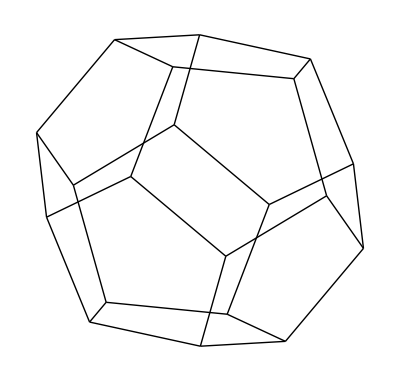

```mathematica
Graphics[Line[Drop[#.rotz[12  Pi/180.].rotx[50π/180.],1]&/@#]&/@(({ϕ,0,1/ϕ}.#&/@{refz,ℐ})⊗({ℐ,refx}⊙rot3⊙rot5))]
```

## Tests

```mathematica
curly=Append[#,√(1-#.#)]& /@ Table[.2{t Cos[9 t],t Sin[9 t]}+{.3,.4},{t,0,1,.02}];
```

```mathematica
Show[Graphics3D[Line[curly]]]
```

-Graphics3D-

```mathematica
mask=ParametricPlot3D[{.99 Cos[u]Sin[v],.99Sin[u]Sin[v],.99Cos[v],{FaceForm[GrayLevel[1]],EdgeForm[]}},
			{u,0,2Pi},{v,0,Pi},Lighting->False,Boxed->False,Axes->False,DisplayFunction->Identity];
```

```mathematica
stest[name_]:=Show[
	Graphics3D[Line /@  
		((curly .#) & /@  Subscript[G, name]),Boxed->False
		
		]]
```

```mathematica
sstest[name_]:=Show[mask,	
		Graphics3D[Line /@  
		((curly .#) & /@  Subscript[G, name]),Boxed->False,DisplayFunction->Identity],
		DisplayFunction->$DisplayFunction]
```

```mathematica
cosetest[name_,gp_]:=Show[mask,	
		Graphics3D[Join @@ Table[{Hue[Random[]],
				
				(Line /@  
		((curly .#) & /@  (Subscript[G, name]⊙{gp[[i]]})))},{i,1,Length[gp]}],Boxed->False,DisplayFunction->Identity],
		DisplayFunction->$DisplayFunction]
```

```mathematica
stest["*222"]
```

-Graphics3D-

```mathematica
cosetest["*222",rot3]
```

-Graphics3D-

```mathematica
sstest["3*2"]
```

-Graphics3D-

```mathematica
sstest["432"]
```

-Graphics3D-

```mathematica
sstest["*432"]
```

-Graphics3D-

```mathematica
sstest["532"]
```

-Graphics3D-

```mathematica
sstest["*532"]
```

-Graphics3D-

## Examples

### Other Examples

#### examples of other projections

```mathematica
swirl=sswirl[3,2.3,100,rot[-Pi/6].scale[.4].trans[{.050,0}]];

sphswirl=pl2sp /@ (homo2cart /@ swirl);
sphpoly:=sphswirl
```

```mathematica
Table[Show[Graphics[
		
		
		
		
		Line /@ (
						stereo ⋆(	(sphpoly .#) & /@  (Subscript[G, "532"]⊙{rotx[.010121].roty[Pi/40 k]}//N)))
								
				
	
			
			
			
			,AspectRatio->Automatic,PlotRange->3{{-1,1},{-1,1}},Axes->False]],{k,0,39}]
```

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Show[Graphics[
		
		
		
		
		Line /@ (homo2cart ⋆  (Join @@
						(abovelist[#,{0,0,1},Identity]&/@((	(sphpoly .#) & /@  (Subscript[G, "532"]⊙{rotx[.010121].roty[Pi/40 k]}//N))))))
								
				
	
			
			
			
			,AspectRatio->Automatic,PlotRange->5{{-1,1},{-1,1}},Axes->False]],{k,1,1}]
```

Less::nord: Invalid comparison with 0.0458568+1.48545×10^-8 ⅈ attempted.

Greater::nord: Invalid comparison with 0.0458568+1.48545×10^-8 ⅈ attempted.

Less::nord: Invalid comparison with 0.23333+1.17314×10^-8 ⅈ attempted.

Greater::nord: Invalid comparison with 0.23333+1.17314×10^-8 ⅈ attempted.

Less::nord: Invalid comparison with -0.299568+6.52784×10^-9 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -0.299568+6.52784×10^-9 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

LessEqual::nord: Invalid comparison with -0.299568+6.52784×10^-9 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with -0.299568+6.52784×10^-9 ⅈ attempted.

LessEqual::nord: Invalid comparison with -0.816389+6.43493×10^-9 ⅈ attempted.

GreaterEqual::nord: Invalid comparison with -0.816389+6.43493×10^-9 ⅈ attempted.

LessEqual::nord: Invalid comparison with -0.602905+1.15811×10^-8 ⅈ attempted.

General::stop: Further output of LessEqual::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with -0.602905+1.15811×10^-8 ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Which::argct: Which called with 5 arguments.

$Aborted

```mathematica
Table[Show[Graphics[
		
		
		
		
		Line /@ (homo2cart ⋆ (Join @@ 
								(abovelist[#,{1,0,4},Identity]& /@ (Join @@
						(abovelist[#,{0,0,1},Identity]&/@((	(sphpoly .#) & /@  (Subscript[G, "532"]⊙{rotx[.010121].roty[Pi/40 k]}//N))))))))
								
				
	
			
			
			
			,AspectRatio->Automatic,PlotRange->5{{-1,1},{-1,1}},Axes->False]],{k,1,1}]
```

{⁃Graphics⁃}

```mathematica
abovelist[sss[[45]],{1,2,1},#&];
```

#### First Examples

```mathematica
swirl=sswirl[3.3,1.3,120,trans[{.6,.85}].scale[{.21,.24}].rot[-70 π/180]];
Show[Graphics[{Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/50}]],
			
			Line[homo2cart /@ swirl]},AspectRatio->Automatic,Axes->True]];
sphpoly=pl2sp /@ (homo2cart /@ swirl);
```

```mathematica
swirl=sswirl[3.3,1.3,120,trans[{.6,.85}].scale[1.9{.21,.24}].trans[{-.01,-.01}].rot[-70 π/180].rot[-.04π]];
Show[Graphics[{Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/50}]],
			
			Line[homo2cart /@ swirl]},AspectRatio->Automatic,Axes->True]];

sphpoly=pl2sp /@ (homo2cart /@ swirl);
```

```mathematica
swirl=sswirl[5,.6,120,scale[{.2,.2}].trans[{.17,.09}].rot[-π  .3].scale[{1.1,.75}].trans[{.03,0 .01}]];
Show[Graphics[{Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/50}]],
			
			Line[homo2cart /@ swirl]},AspectRatio->Automatic,Axes->True]];
sphpoly=pl2sp /@ (homo2cart /@ swirl);
```

```mathematica
sphtest["3*2",-{1,1,1},rot5]
```

⁃Graphics⁃

```mathematica
sphtest["3*2",{1,1,1},rot5]
```

⁃Graphics⁃

```mathematica
sphtest["332",5{1,1,1},rot5]
```

⁃Graphics⁃

```mathematica
sphtest["332",-5{1,1,1},rot5]
```

⁃Graphics⁃

## For the Book

### Symmetry groups

```mathematica
defaultNumSegs=80;
Subscript[sPoly, "*432"]=
	pl2sp /@ (homo2cart /@ sswirl[4.3,1.3,defaultNumSegs,trans[{1,0}].scale[.27].rot[77 π/180].scale[{1,1.5}].trans[{0,.12}]]);



Subscript[sPoly, "432"]=pl2sp /@ (homo2cart /@ sswirl[4.3,1.3,defaultNumSegs,trans[{1,0}].scale[.5].rot[77 π/180].trans[{0,.08}]]);




Subscript[sPoly, "3*2"]=pl2sp /@ (homo2cart /@
				sswirl[4.3,1.3,defaultNumSegs,trans[{1,0}].scale[.5].rot[77 π/180].trans[{0.04,.04}]]
			);

Subscript[sPoly, "*532"]=pl2sp /@ (homo2cart /@
				sswirl[3.3,1.3,defaultNumSegs,trans[{.6,.85}].scale[{.21,.24}].rot[-70 π/180]]
			);

Subscript[sPoly, "532"]=pl2sp /@ (homo2cart /@
				sswirl[3.3,1.3,defaultNumSegs,rot[30 π/180.].trans[{.6,.75}].scale[1.5{.21,.24}].rot[-70 π/180]]
			);

Subscript[sPoly, "332"]=pl2sp /@ (homo2cart /@
sswirl[3.8,1.3,defaultNumSegs,rot[0 π/180.].trans[0{.6,.75}].scale[3.4{.21,.24}].rot[0  70 π/180]]
			);


Subscript[sPoly, "*332"]= #.rotz[45  Pi/180.].rotx[0π/180.].roty[0π/180.]&/@(pl2sp /@ (homo2cart /@
				sswirl[3.3,1.3,defaultNumSegs,trans[{.6,.85}].scale[1.6{.21,.24}].rot[-65 π/180].trans[0{-.71,0}].scale[1.4]])
			);

Subscript[sPoly, "12x"]= #.rotz[240  Pi/180.].rotx[52 π/180.]&/@
		
		(pl2sp /@ (homo2cart /@
				sswirl[3.3,1.3,defaultNumSegs,trans[{.6,.85}].scale[2.2{.21,.24}].rot[-65 π/180].trans[0{-.5,.3}]]
			));


			
Subscript[sPoly, "*228"]=#.rotz[90  Pi/180.].rotx[90 π/180.]&/@(pl2sp /@ (homo2cart /@
				sswirl[3.3,1.3,defaultNumSegs,trans[{.6,.85}].scale[2.2{.21,.24}].rot[-65 π/180].trans[0{-.5,.3}].scale[{.95,.85}]]
			));

Subscript[sPoly, "*88"]=#.rotz[90  Pi/180.].rotx[110π/180.]&/@(pl2sp /@ (homo2cart /@
				sswirl[3.3,1.3,defaultNumSegs,trans[{.6,.85}].scale[2.2{.21,.24}].rot[-65 π/180].trans[0{-.5,.3}].scale[{1.1,.85}]]
			));

Subscript[sPoly, "1616"]=#.rotz[90  Pi/180.].rotx[110π/180.]&/@(pl2sp /@ (homo2cart /@
				sswirl[3.4,1.3,defaultNumSegs,trans[{.6,.85}].scale[2.2{.21,.24}].rot[-65 π/180].trans[0{-.5,.3}].scale[1{.95,.85}]]
			));

Subscript[sPoly, "12*"]=#.rotz[93  Pi/180.].rotx[90 π/180.]&/@(pl2sp /@ (homo2cart /@
				sswirl[3.3,1.3,defaultNumSegs,trans[{.6,.85}].scale[2.2{.21,.24}].rot[-65 π/180].trans[0{-.5,.3}].scale[{1,1}]]
			));

Subscript[sPoly, "2212"]=#.rotz[100  Pi/180.].rotx[97 π/180.]&/@(pl2sp /@ (homo2cart /@
				sswirl[3.5,1.2,defaultNumSegs,trans[{.6,.85}].scale[2.2{.21,.24}].rot[-65 π/180].trans[0{-.5,.3}].scale[{1,1}]]
			));

Subscript[sPoly, "2*7"]=#.rotz[116 Pi/180.].roty[67 π/180].rotx[91π/180.]&/@
		(pl2sp /@ (homo2cart /@
				sswirl[3.5,1.2,defaultNumSegs,trans[{.6,.85}].scale[2.2{.21,.24}].rot[-65 π/180].trans[0{-.5,.3}].scale[.73{1.1,1}]]
			));
```

```mathematica
Subscript[G, "*22n",8];		
	Subscript[G, "22x",12];
	Subscript[G, "*nn",8];	
Subscript[G, "nn",16];
Subscript[G, "22n",12];
Subscript[G, "n*",12];
Subscript[G, "2*n",7];
```

```mathematica
sphGpList={"332","3*2","*332","432","*432","532","*532","1616","*88","12*","12x","2*7","*228","2212"};
```

```mathematica
vvp={1,.2,1};
{vP["332"]={1.7,.5,.5},
		vP["3*2"]={1.7,.5,.5},
	vP["*332"]={1.7,.5,.5},
	
	
vP["432"]={2,1.5,1.7},
		vP["*432"]={2,1.5,1.7},
	
	vP["532"]={1.6,1.05,.1},
	vP["*532"]={1.6,1.05,.1},

		vP["1616"]={1,2,1},
		vP["*88"]={1,2,1},
	vP["12*"]={1,2,1},


	vP["12x"]={1,2,1},
		vP["2*7"]={1,2,1},

				
	vP["*228"]={1,2,1},
	vP["2212"]={1,2,1},
	};
```

A few more colorings

```mathematica
Subscript[G, "22n",4];
swirl=sswirl[4.3,1.3,defaultNumSegs,trans[{1,0}].scale[.5].rot[77 π/180].trans[{0,.08}]];
sphpoly=pl2sp /@ (homo2cart /@ swirl);
sphtest["224",{1,1,1},rot3]
```

⁃Graphics⁃

```mathematica
Subscript[G, "*22n",4];
swirl=sswirl[4.3,1.3,defaultNumSegs,trans[{1,0}].scale[.27].rot[77 π/180].scale[{1,1.5}].trans[{0,.12}]];
sphpoly=pl2sp /@ (homo2cart /@ swirl);
sphtest["*224",vP["*432"],rot3]
```

⁃Graphics⁃

```mathematica
Subscript[G, "*22n",2];
swirl=sswirl[4.3,1.3,defaultNumSegs,trans[{1,0}].scale[.5].rot[77 π/180].trans[{0.04,.04}]];
sphpoly=pl2sp /@ (homo2cart /@ swirl);
sphtest["*222",vP["3*2"],rot3]
```

⁃Graphics⁃

```mathematica
Subscript[G, "22n",2];
swirl=sswirl[3.8,1.3,defaultNumSegs,rot[0 π/180.].trans[0{.6,.75}].scale[3.4{.21,.24}].rot[0  70 π/180]];
sphpoly=pl2sp /@ (homo2cart /@ swirl);
sphtest["222",vP["332"],rot3]
```

⁃Graphics⁃

### Pictures of Spherical Groups

```mathematica
dbleSphtest[#,vP[#]]&/@sphGpList
```

$Aborted

```mathematica
Show[GraphicsArray[
	Table[dbleSphtest[sphGpList⟦i+7j⟧,
			
			vP[sphGpList⟦i+7j⟧],DisplayFunction->Identity],{j,0,1},{i,1,7}]],DisplayFunction->$DisplayFunction]
```

⁃GraphicsArray⁃

### Heesch Types

#### A little prepwork

```mathematica
vvp={1,.2,1};
{vP["332"]={1.7,.5,.5},
		vP["3*2"]={1.7,.5,.5},
	vP["*332"]={1.7,.5,.5},
	
	
vP["432"]={2,1.5,1.7},
		vP["*432"]={2,1.5,1.7},
	
	vP["532"]={1.6,1.05,.1},
	vP["*532"]={1.6,1.05,.1},

		vP["1616"]={1,2,1},
		vP["*88"]={1,2,1},
	vP["12*"]={1,2,1},


	vP["12x"]={1,2,1},
		vP["2*7"]={1,2,1},

				
	vP["*228"]={1,2,1},
	vP["2212"]={1,2,1},
	};
```

```mathematica
Subscript[G, "*22n",8];		
	Subscript[G, "nx",12];
	Subscript[G, "*nn",8];	
Subscript[G, "nn",16];
Subscript[G, "22n",12];
Subscript[G, "n*",12];
Subscript[G, "2*n",7];
```

```mathematica
Subscript[G, "22n",8];
```

#### The main command

```mathematica
PlotHeesch[
	name_,
	corners_,
	MM_,
	centerV_,
	splineVectors_,
	additionalCurves_,
	view_,
{showFullQ_, showSplineOnlyQ_}]:=
	
(
	cc=Append[#,OverBar[centerV.#]]&[corners];
		cd=stereo[MM.#]&/@ cc;
		ss=#&/@(
					spline[cd⟦#⟦1,1⟧⟧,cd⟦#⟦1,2⟧⟧,#⟦2,1⟧.cd, #⟦2,2⟧.cd]&/@
					splineVectors);
					
					pd=Table[#,{t,0,1,.05}]&/@ss;
					
					vv=OverBar[view]; bb=OverBar[{-vv⟦2⟧,vv⟦1⟧,0}];
					
				
pp=Join[Table[Chop[stereo2sphere[#],10^-6],{t,0,1,.02}]&/@ss,additionalCurves];
				
			If[showFullQ===1|| showFullQ===True,	Show[Graphics[Join[{Hue[.1],Circle[{0,0},1], Thickness[.01]},
			
			
			Table[Join[{GrayLevel[i/(Length[pp]+1)]},
			
			Line/@(Join @@(FlatSphereCurve[
			#,vv,bb]&/@((Join @@((# ⊗ Subscript[G, name])&/@{pp⟦i⟧})))))],{i,1,Length[pp]}]],AspectRatio->Automatic, PlotRange->All]]];
		
		If[showSplineOnlyQ===1|| showSplineOnlyQ===True,
			
		i=1;Show[Graphics[Join[{Hue[.1],Circle[{0,0},.99],PointSize[.02], Thickness[.01]},Point/@cd,Join[{GrayLevel[(i++)/4],Line[#]}&] /@pd],AspectRatio->Automatic,PlotRange->All]]
		
		]
					);
```

#### THE WORK

```mathematica
PlotHeesch["432",{OverBar[{0,0,1}],OverBar[{0,1,1}],OverBar[{1,1,1}]},rotx[π], OverBar[{2,1,1.2}],
	{
		{ {1,4},{{0,0,0,0},{0,0,0,0}}},
		{ {2,4},{{1,-1,0,0},{.5,.5,0,-1}}},
		{ {3,4},{{1,0,-1,0},-{.5,.5,0,-1}}}
	},{}
	,
	vP["432"],{1,0}]
```

```mathematica
PlotHeesch["432",{OverBar[{0,0,1}],OverBar[{0,1,1}],OverBar[{1,1,1}]},rotx[π],OverBar[{2,1,1.2}],
	{
		{ {1,2},{{-1,-1,1,1}, {0,-1,0,1}}},
		{ {2,3},{{1,-2,1,0},.5{1,-1,0,0}}},
		{ {3,1},{1.5{1,-1,0,0},-{.5,.5,0,-1}}}
	},{}
	,
	vP["432"],{1,0}]
```

```mathematica
PlotHeesch["532",{OverBar[{1,0,ϕ}],{0,0,1},OverBar[{0,τ,ϕ}]},rotx[π],OverBar[{1.5,1,2}],
	{
		{ {1,4},{{0,0,0,0},2 {0,-1,-1,2}}},
		{ {2,4},{{1,-1,0,0},{.5,.5,0,-1}}},
		{ {3,4},{{1,0,-1,0},-{.5,.5,0,-1}}}
	},{}
	,
	vP["532"],{1,0}]
```

```mathematica
PlotHeesch["532",{OverBar[{1,0,ϕ}],{0,0,1},OverBar[{0,τ,ϕ}]},rotx[π],OverBar[{3,3,2}],
	{
	},{Subscript[sPoly, "*532"], #.refz&/@ Subscript[sPoly, "*532"], GreatCircle[OverBar[{1,0,ϕ}],{0,0,1},10], GreatCircle[OverBar[{1,0,ϕ}],OverBar[{0,τ,ϕ}],10], GreatCircle[OverBar[{0,τ,ϕ}],{0,0,1},10]}
	,
	vP["532"],{1,0}]
```

```mathematica
PlotHeesch["432",{OverBar[{0,0,1}],OverBar[{0,1,1}],OverBar[{1,1,1}]},rotx[π],OverBar[{2,1,1.2}],
	{
	
	},{Subscript[sPoly, "*432"], #.refz&/@ Subscript[sPoly, "*432"], 
		GreatCircle[OverBar[{0,1,1}],{0,0,1},10],
	GreatCircle[OverBar[{1,1,1}],{0,0,1},10],
	GreatCircle[OverBar[{0,1,1}],OverBar[{1,1,1}],10]}
	,
	vP["*432"],{1,0}]
```

```mathematica
PlotHeesch["332",{OverBar[{0,0,1}],OverBar[{-1,1,1}],OverBar[{1,1,1}]},rotx[π], OverBar[{2,1,1}],
	{
	},{Subscript[sPoly, "*332"], #.{{0,1,0},{1,0,0},{0,0,1}}&/@ Subscript[sPoly, "*332"],GreatCircle[OverBar[{0,0,1}],OverBar[{-1,1,1}],10],GreatCircle[OverBar[{0,0,1}],OverBar[{1,1,1}],10],GreatCircle[OverBar[{1,1,1}],OverBar[{-1,1,1}],10]}
	,
	vP["332"],{1,0}]
```

```mathematica
PlotHeesch["532",{OverBar[{1,0,ϕ}],{0,0,1},OverBar[{0,τ,ϕ}]},rotx[π],OverBar[{3,3,2}],
	{
		{ {1,2},{{-1,-1,1,1}, {0,-1,0,1}}},
		{ {2,3},{{1,-2,1,0},.5{1,-1,0,0}}},
		{ {3,1},{1.5{1,-1,0,0},-{.5,.5,0,-1}}}
	},{}
	,
	vP["532"],{1,0}]
```

```mathematica
PlotHeesch["332",{OverBar[{0,0,1}],OverBar[{-1,1,1}],OverBar[{1,1,1}]},rotx[π], OverBar[{2,1,1}],
	{
	{{2,4},{{1,-1,0,0},{.5,.5,0,-1}}},
		{ {3,4},{{1,0,-1,0},-{.5,.5,0,-1}}}
	},{GreatCircle[{1,0,0},{0,0,1},10]
			
			}
	,
		{.6,-2,1},{1,0}]
```

```mathematica
PlotHeesch["332",{OverBar[{0,0,1}],OverBar[{-1,1,1}],OverBar[{1,1,1}]},rotx[π], OverBar[{2,1,1}],
	{
		{ {1,4},{{0,0,0,0},0{0,-1,-1,2}}},
		{ {2,4},{{1,-1,0,0},{.5,.5,0,-1}}},
		{ {3,4},{{1,0,-1,0},-{.5,.5,0,-1}}}
	},{}
	,
	vP["332"],{1,0}]
```

```mathematica
PlotHeesch["332",{OverBar[{0,0,1}],OverBar[{-1,1,1}],OverBar[{1,1,1}]},rotx[π], OverBar[{2,1,2}],
	{
		{ {1,4},{{0,0,0,0},0{0,-1,-1,2}}},
		{ {2,4},{{1,-1,0,0},{.5,.5,0,-1}}},
		{ {3,4},{{1,0,-1,0},-{.5,.5,0,-1}}}
	},{}
	,
	vP["332"],{1,0}]
```

```mathematica
PlotHeesch["332",{OverBar[{-1,1,1}],OverBar[{0,0,1}],OverBar[{1,1,1}]},rotx[π], OverBar[{2,1,2}],
	{
		{ {1,4},{{0,0,0,0},1 {0,-1,-1,2}}},
		{ {2,4},{{1,-1,0,0},{.5,.5,0,-1}}},
		{ {3,4},{{1,0,-1,0},-{.5,.5,0,-1}}}
	},{}
	,
	{.7,.3,.6},{1,0}]
```

```mathematica
PlotHeesch["332",{OverBar[{-1,1,1}],OverBar[{0,0,1}],OverBar[{1,1,1}]},rotx[π], OverBar[{2,1,2}],
	{
		{ {1,2},{.3{-1,-1,1,1},0 {0,-1,0,1}}},
		{ {2,3},{{1,-2,1,0},{1,-1,0,0}}},
		{ {3,1},{1.5{1,-2,1,0},{1,-2,1,0}}}
	},{}
	,
	{1,-1,3},{1,0}]
```

```mathematica
PlotHeesch["2212",{OverBar[{1,0,0}],OverBar[{0,0,1}],OverBar[{Cos[π/12],Sin[π/12],0}]},rotx[π], OverBar[{1,1,1}],
	{
		{ {1,2},{0{-1,1,0,0},3{1,0,-1,0}+{1,0,0,-1}}},
		{ {2,3},{3{1,0,-1,0}+{1,0,0,-1},.5{1,0,-1,0}+1{0,0,-1,1}}},
		{ {3,1},{{0,0,0,0},{-2,-1,3,0}}}
	},{}
	,
	{6,4,3},{1,1}]
```

⁃Graphics⁃

```mathematica
PlotHeesch["2212",{OverBar[{0,0,1}],OverBar[{01,0,0}],OverBar[{Cos[π/12],Sin[π/12],0}]}, rotx[π],OverBar[{2,1,1}],
		{
		{ {1,4},{1{0,1,-1,0}+.5{0,1,0,-1},1{0,1,-1,0}+.5{0,0,-1,1}}},
		{ {2,4},{0 .5{0,-1,1,0}+0 {0,-1,0,1},-2{0,1,-1,0}-1{0,0,-1,1}}},
		{ {3,4},{0{1,0,-1,0},-2{0,1,-1,0}-1{0,0,-1,1}}}
	},{}
	,
	{6,4,3},{1,1}]
```

⁃Graphics⁃

```mathematica
PlotHeesch["12*",{OverBar[{0,0,1}],OverBar[{01,0,0}],OverBar[{Cos[π/6],Sin[π/6],0}]},rotx[π], OverBar[{0,1.3,1}],
		{
		{ {1,4},{1{0,1,-1,0}+.5{0,1,0,-1},{1,0,0,-1}}}
	},{Table[{Cos[k π/6 /10],Sin[k π/6 /10],0},{k,0,10}]}
	,
	{6,4,3},{1,1}]
```

⁃Graphics⁃

```mathematica
PlotHeesch["12x",{OverBar[{0,0,1}],OverBar[{01,0,.5}],OverBar[{Cos[π/12],Sin[π/12],-.5}]},rotx[π], {1,1,1},
		{
		{ {1,2},{-2{0,1.1,-.1,-1},-2{-1,1,0,0}}},
		{ {2,3},{2{-1,1,0,0},10{0,1.1,-.1,-1}}}
	},{}
	,
	{6,4,3},{1,1}]
```

⁃Graphics⁃

```mathematica
PlotHeesch["12x",{OverBar[{0,0,1}],OverBar[{01,0,0}],OverBar[{Cos[π/12],Sin[π/12],0}],OverBar[{Cos[π/24],Sin[π/24],0}],OverBar[{Cos[π/8],Sin[π/8],0}]},rotx[π], {1,1,1,0,0},
		{
		{ {1,2},{3{0,-1,0,1,0,0},3{0,-1,0,1,0,0}}},
		{ {1,3},{3{0,-1,0,1,0,0},3{0,0,-1,1,0,0}}}
	},{}
	,
	{6,4,3},{1,1}]
```

⁃Graphics⁃

```mathematica
PlotHeesch["2*7",{OverBar[{0,0,1}],OverBar[{0,1,.5}],OverBar[{Sin[π/7],Cos[π/7],-.5}],OverBar[{Sin[π/14],Cos[π/14],0}]},rotx[π], {1,1,1,0},
		{
		{ {1,2},{{0,0,0,0,0},{0,0,0,0,0}}},
		{ {1,3},{{0,0,0,0,0},{0,0,0,0,0}}},
		{ {2,4},{2{0,-1,0,0,1},{0,0,0,0,0}}}
	},{}
	,
	{6,4,3},{1,1}]
```

⁃Graphics⁃

```mathematica
PlotHeesch["2*7",{OverBar[{0,0,1}],OverBar[{0,1,0}],OverBar[{Sin[π/7],Cos[π/7],0}],OverBar[{Sin[π/14],Cos[π/14],0}]},rotx[π], {1,1,1,0},
		{
		{ {1,2},{{0,0,0,0,0},{0,0,0,0,0}}},
		{ {1,3},{{0,0,0,0,0},{0,0,0,0,0}}},
		{ {1,4},{.2{0,1,-1,0,0},1.5{0,-1,1,0,0}+{0,0,0,-1,1}}}
	},{}
	,
	{6,4,3},{1,1}]
```

⁃Graphics⁃

```mathematica
Subscript[G, "nnB",n_]:=Subscript[G, #<>#&[ToString[n]]<>"B"]=Subscript[(rot[{0,1,0},2Pi/n]), n]//N;
```

```mathematica
Subscript[G, "*nnB",n_]:=Subscript[G, "*"<>#<>#&[ToString[n]]<>"B"]=Subscript[G, "nnB",n]⊙{ℐ,refy};
```

```mathematica
Subscript[G, "nnB",15];
```

```mathematica
Subscript[G, "*nnB",8];
```

```mathematica
PlotHeesch["1515B",{OverBar[{0,0,-1}],OverBar[{0,0,1}],OverBar[{Sin[π/16],Cos[π/16],0}], OverBar[{-Sin[π/16],Cos[π/16],0}]},rotx[π/2], OverBar[{1,1,1,1}],
	{
		{{1,2},{5{0,0,1,-1,0},{.2,-.2,-10,10,0}}}
	
	},{}
	,
	{6,2,3},{1,1}]
```

⁃Graphics⁃

```mathematica
PlotHeesch["3*2",{OverBar[{-1,1,1}],OverBar[{0,0,1}],OverBar[{1,1,1}]},rotx[π], OverBar[{2,1,2}],
	{
		{ {1,2},{{-2,-.3,.3,2},0 {0,-1,0,1}}}
	
	},{GreatCircle[{1,0,0},{0,1,0},10]}
	,
	{2,.6,1},{1,0}]
```

```mathematica
PlotHeesch["3*2",{OverBar[{-1,1,1}],OverBar[{0,0,1}],OverBar[{-1,0,0}]},rotx[π], OverBar[{0,.5,2}],
	{
		{ {1,4},{{-2,.5,.5,2}, .1{3,-2,-1,0}}}
	
	},{GreatCircle[{1,0,0},{0,1,0},10]}
	,
	{.6,-2,1},{1,1}]
```

⁃Graphics⁃

```mathematica
PlotHeesch["228",{OverBar[{0,0,1}],OverBar[{0,1,0}],OverBar[{Cos[π/8],Sin[π/8],0}]},rotx[π],OverBar[{2,1,1.2}],
	{
	
	},{
		GreatCircle[{0,0,1},{0,1,0},10],
	GreatCircle[{Cos[π/8],Sin[π/8],0},{0,0,1},10],
	GreatCircle[{Cos[π/8],Sin[π/8],0},{0,1,0},10],
	
	
	
	 Subscript[sPoly, "*228"],#.refy&/@ Subscript[sPoly, "*228"]
	
	}
	,
	vP["*432"],{1,0}]
```

```mathematica
PlotHeesch["228",{OverBar[{0,0,1}],OverBar[{0,1,0}],OverBar[{Cos[π/8],Sin[π/8],0}]},rotx[π],OverBar[{2,1,1.2}],
	{
	
	},{
		GreatCircle[{0,0,1},{0,1,0},10],
	GreatCircle[{Cos[π/8],Sin[π/8],0},{0,0,1},10],
	
	
	
	 Subscript[sPoly, "*88"],#.refy&/@ Subscript[sPoly, "*88"]
	
	}
	,
	vP["*432"],{1,0}]
```

#### the old way

```mathematica
Subscript[c, "332"]={OverBar[{-1,1,1}],OverBar[{0,0,1}],OverBar[{1,1,1}]};
```

```mathematica
cc=Append[#,OverBar[{0,.4,.9}]]&[Subscript[c, "332"]]
```

{{-0.57735,0.57735,0.57735},{0,0,1.},{0.57735,0.57735,0.57735},{0,0.406138,0.913812}}

```mathematica
cd=stereo[rotx[π].#]&/@ cc
```

{{-0.366025,-0.366025},{0.,0.},{0.366025,-0.366025},{0.,-0.212214}}

```mathematica
ss=#&/@{
			spline[  cd⟦1⟧,cd⟦4⟧,{0,0},{0,-.3}],
			spline[  cd⟦2⟧,cd⟦4⟧,0{.1,-.1},{.1,.3}],
			spline[  cd⟦3⟧,cd⟦4⟧, {-.1,.10},{0,-.3}]
	};

pd=Table[#,{t,0,1,.05}]&/@ss;
```

```mathematica
pp=Table[Chop[stereo2sphere[#],10^-6],{t,0,1,.02}]&/@ss;
```

```mathematica
Show[Graphics[Join[{Hue[.1],Circle[{0,0},1]},
			
			
			Table[Join[{Thickness[.01],GrayLevel[i/4]},
			
			Line/@(Join @@(FlatSphereCurve[
			#,OverBar[{1,1,3}],OverBar[{-1,-1,2/3}]]&/@((Join @@((# ⊗ Subscript[G, "332"])&/@{pp⟦i⟧})))))],{i,1,3}]],AspectRatio->Automatic, PlotRange->All]]
```

⁃Graphics⁃

### A couple of graphs

```mathematica
ssphere={Cos[v],Cos[u] Sin[v],Sin[u] Sin[v]};

ss1 = Table[ssphere/.{v->Pi/15,u->uu},{uu,0,2Pi,Pi/20}];

ss2=Table[ssphere /. {v->vv,u->0},{vv,Pi/15,2Pi/9-Pi/15,Pi/135}];

ss3 = (Table[ssphere /.{v->Pi/80,u->uu},{uu,0,2Pi,2Pi/10}]⊗({rotz[Pi/15.],rotz[-Pi/15.]}));
```

OverBar[-{a,b,c}],	OverBar[-{-b,a,0}] for backs

```mathematica
vv=OverBar[{1,0,-.4}];
bb=OverBar[{0,-1,0}];	

vvBack =
	Show[Graphics[{
			
			Line/@(Join @@(FlatSphereCurve[#,vv,bb]&/@ (ss1⊗Subscript[G, "nn",9]))),
				
			Line/@(Join @@(FlatSphereCurve[#,vv,bb]&/@ (ss2⊗Subscript[G, "nn",9]))),
			
			Hue[.5],
			
			Line/@(Join @@(FlatSphereCurve[#,vv,bb]&/@ (ss3⊙Subscript[G, "nn",9]))),
				
				GrayLevel[.5],
				
				Line/@(Join @@(FlatSphereCurve[#,-vv,-bb]&/@ (ss1⊗Subscript[G, "nn",9]))),
				
			Line/@(Join @@(FlatSphereCurve[#,-vv,-bb]&/@ (ss2⊗Subscript[G, "nn",9]))),
			
			GrayLevel[.7],
			
			Line/@(Join @@(FlatSphereCurve[#,-vv,-bb]&/@ (ss3⊙Subscript[G, "nn",9]))),
			
			Hue[.4],Circle[{0,0},1]},
		
		AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
vvBack =
	Show[Graphics[{
			
			
			
			Line/@(Join @@(FlatSphereCurve[#,vv,bb]&/@ (ss3[[{1}]]⊙
											Table[rot[{Random[Real,{-1,1}],Random[Real,{-1,1}],Random[Real,{-1,1}]},Random[] 2Pi],{i,1,200}]
												
									))),
			
			Hue[.4],Circle[{0,0},1]},
		
		AspectRatio->Automatic,PlotRange->All]]
```

⁃Graphics⁃

### Other Examples

#### For subgps of *224

```mathematica
move= trans[{.6,.85}].scale[2{.21,.24}].rot[-65 π/180].trans[0{-.5,.3}].scale[{.95,.85}];


move= trans[{.9,1.3}].scale[2.4{.21,.24}].rot[-65 π/180].scale[{.85,.85}];



Subscript[sPoly, "*224"]=(pl2sp /@ (homo2cart /@
				sswirl[3.3,1.3,defaultNumSegs,move
							
							]
			));
Subscript[G, "*22n",4];
	vP["*224"]={.1,.05,1};
dbleSphtest["*224",vP["*224"]];
```

```mathematica
move= trans[{.6,.85}].scale[2{.21,.24}].rot[-65 π/180].trans[0{-.5,.3}].scale[{.95,.85}];


move= trans[{1,1.3}].scale[2.4{.21,.24}].rot[-65 π/180].scale[{.85,.85}];



Subscript[sPoly, "*224"]=(pl2sp /@ (homo2cart /@
				sswirl[3.3,1.3,defaultNumSegs,move
							
							]
			));
Subscript[G, "*22n",4];
	vP["*224"]={2,4,3};
dbleSphtest["*224",vP["*224"]];
```

#### Some Movies

```mathematica
Table[

	 dbleSphtest["12x",tt=t*π/96;
					
					
					{1,1.5,2}.{{Cos[tt],Sin[tt],0},{-Sin[tt],Cos[tt],0},{0,0,1}}]
		
		
		
		
		,{t,0,7}]
```

#### Some tiling examples

```mathematica
Subscript[c, "532"]={{0,0,1},OverBar[{1,0,ϕ}],OverBar[{0,τ,ϕ}]};
```

```mathematica
cc=Append[#,OverBar[Plus @@ #]]&[Subscript[c, "532"]]
```

{{0,0,1},{0.525731,0,0.850651},{0,0.356822,0.934172},{0.184054,0.124921,0.974946}}

```mathematica
ss=OverBar[#]&/@{
			spline[  cc⟦1⟧,cc⟦4⟧,0 .6{-1,1,0},{0,0,0}],
			spline[  cc⟦2⟧,cc⟦4⟧,.6{-1,-1,0},{0,0,0}],
			spline[  cc⟦3⟧,cc⟦4⟧,0 1.2{1,0,0},{0,0,0}]
	};

pp=Table[#,{t,0,1,.05}]&/@ss;
```

```mathematica
Show[
	Graphics3D[
		Join[ 
			Line /@(Join @@((# ⊗ Subscript[G, "532"])&/@pp)),
			Point /@ (cc⟦4⟧.#& /@  Subscript[G, "532"]),
		{Hue[.3],PointSize[.04]},
			Point /@ cc 
			(*,{Hue[.5]},Point/@ (OverBar[{1,1 ,1}].#& /@ rot5),
				{Hue[.7]},Point/@(OverBar[{1,0,1}].#& /@ rot3)*)
		],ViewPoint->10{0,0,1},Boxed->False],
	mask,
	DisplayFunction->$DisplayFunction,Lighting->False]
```

⁃Graphics3D⁃

```mathematica
ppoly=Join[
		pp⟦1⟧,
		Reverse[pp[[3]]],
		#. rot5⟦2⟧.rot3⟦-1⟧.rot5⟦5⟧           &/@ pp⟦3⟧,
		#. rot5⟦5⟧.rot4⟦3⟧         &/@ Reverse[pp⟦2⟧],
		#.rot4⟦3⟧         &/@ pp⟦2⟧,
		#.rot4⟦3⟧         &/@ Reverse[pp⟦1⟧]
	
	
	];
```

```mathematica
Show[Graphics3D[Join[{Line[ppoly],Hue[.3],PointSize[.04]},Point /@ cc],ViewPoint->10{0,0,1},Boxed->False],mask,DisplayFunction->$DisplayFunction,Lighting->False]
```

⁃Graphics3D⁃

```mathematica
sphpoly=ppoly;
sphtest["332",5{1,1,1},rot5]
```

⁃Graphics⁃

```mathematica
col=
	(Hue @@#)& /@  
{
	{.23,.5,.7},
			{.35,.5,.7},
			{.17,.5,.7},
			{.43,.5,.7},
			{.54,.5,.7}}
```

{Hue[0.23,0.5,0.7],Hue[0.35,0.5,0.7],Hue[0.17,0.5,0.7],Hue[0.43,0.5,0.7],Hue[0.54,0.5,0.7]}

```mathematica
newsphtest[name_,{a_,b_,c_},cosets_]:=Module[{},Show[i=1;Graphics[Join[
		
		Join @@ ({col[[i++]],#}&/@(Polygon ⋆ ((Join @@  ( FlatSpherePoly[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}],.1]&/@ 
											((sphpoly .#) & /@  (Subscript[G, name]⊙{#}))
									)&/@cosets//N)))),	
				
				{GrayLevel[.5],Line[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/50}]]}
			
			
			
			],AspectRatio->Automatic,Axes->False]]]
```

```mathematica
newsphtest["332",5{1,1,1},rot5]
```

⁃Graphics⁃

```mathematica
newsphtest["332",-5{1,1,1},rot5]
```

⁃Graphics⁃

```mathematica
Sgpwrite[file_,name_]:=
	
(
	
	
	WriteString[file,
			
			
			
			If[commentQ,"\n################",""]<>
				
					"\n \n"<> name<>
					"    "<> ToString[Subscript[atr, name]]<>"\n\n"];
					
					
		WriteString[file,	
				If[commentQ,	"# the fund region\n",""]<>
					ToString[Length[Subscript[fund, name]]]<>"\n"];
					
			Table[WriteString[file,numwrite[Subscript[fund, name]⟦i,1⟧]<>sp<>numwrite[Subscript[fund, name]⟦i,2⟧]<>sp<>numwrite[Subscript[fund, name]⟦i,3⟧]<>"\n"],
				{i,1,Length[Subscript[fund, name]]}];WriteString[file,"\n\n"];
		
	 If[commentQ,WriteString[file,"# the mirror lines and rotation points\n"]];			
	
		WriteString[file,ToString[Length[Subscript[mirlines, name]]]<>"\n"];
		i=0; While[i<Length[Subscript[mirlines, name]],i++;
			WriteString[file,numwrite[Subscript[mirlines, name][[i,1]]]<>"   "<>
					numwrite[Subscript[mirlines, name][[i,2]]]<>sp<>numwrite[Subscript[mirlines, name][[i,3]]]<>"\n"]];
		WriteString[file,"\n"];
	
				WriteString[file,ToString[Length[rotpts[2][name]]]<>"\n"];
				i=0; While[i<Length[rotpts[2][name]],i++;
			WriteString[file,
					numwrite[rotpts[2][name][[i,1]]]<>sp<>numwrite[rotpts[2][name][[i,2]]]<>sp<>numwrite[rotpts[2][name][[i,3]]]<>"\n"]];
		WriteString[file,"\n"];			
		
			WriteString[file,ToString[Length[rotpts[3][name]]]<>"\n"];
		i=0; While[i<Length[rotpts[3][name]],i++;
			WriteString[file,
					numwrite[rotpts[3][name][[i,1]]]<>sp<>numwrite[rotpts[3][name][[i,2]]]<>sp<>numwrite[rotpts[3][name][[i,3]]]<>"\n"]];
		WriteString[file,"\n"];			
					
			WriteString[file,ToString[Length[rotpts[4][name]]]<>"\n"];
		i=0; While[i<Length[rotpts[4][name]],i++;
			WriteString[file,
					numwrite[rotpts[4][name][[i,1]]]<>sp<>numwrite[rotpts[4][name][[i,2]]]<>sp<>numwrite[rotpts[4][name][[i,3]]]<>"\n"]];
		WriteString[file,"\n"];			
				
				WriteString[file,ToString[Length[rotpts[5][name]]]<>"\n"];	
		i=0; While[i<Length[rotpts[5][name]],i++;
			WriteString[file,
					numwrite[rotpts[5][name][[i,1]]]<>sp<>numwrite[rotpts[5][name][[i,2]]]<>sp<>numwrite[rotpts[5][name][[i,3]]]<>"\n"]];
		
					If[commentQ,WriteString[file,"\n\n# the transforms\n"]];	
			WriteString[file,
				"\n"<>ToString[Length[Subscript[G, name]]]<>sp<>
			"\n\n"];
				Table[matwrite[file,Subscript[G, name]⟦i⟧],{i,1,Length[Subscript[G, name]]}];
	WriteString[file,"\n\n"]
			
			)
```

```mathematica
WriteString[file, ToString[Length[sphericalgps]]<>"\n"];

Sgpwrite[file,#]&/@sphericalgps;Close[file]
```

Sally:Desktop Folder:SphericalSymmetries.txt

### The Cayley Graph of 532

Lets really get this looking good. First

```mathematica
Off[ParametricPlot3D::"ppcom"]
```

```mathematica
pp=OverBar[OverBar[{.5,.2,.3}].{OverBar[{ϕ,1,0}],OverBar[{ϕ,-1,0}],OverBar[{ϕ,0,τ}]}];
```

```mathematica
verts=OverBar[pp.#]&/@{ℐ,rot[{1,0,0},π],rot[{ϕ,0,τ},2π/3],rot[{ϕ,1,0},2π/5]};
```

```mathematica
Show[
	
	Graphics3D[Join [
			Line/@({verts⟦1⟧,verts⟦2⟧}⊗ Subscript[G, "532"]//N),
			Line/@({verts⟦1⟧,verts⟦3⟧}⊗ Subscript[G, "532"]//N),
			Line/@({verts⟦1⟧,verts⟦4⟧}⊗ Subscript[G, "532"]//N)
			
		
		]],
	
	ParametricPlot3D[Append[.7{Sin[u]Cos[v],Cos[u]Cos[v],Sin[v]},EdgeForm[]],{v,-π/2,π/2},{u,0,2π},DisplayFunction->Identity]
	
	
	
	,Boxed->False,DisplayFunction->$DisplayFunction]
```

⁃Graphics3D⁃

```mathematica
cc=Table[(#/.{t->tt})//Chop[#,10^-5]&//(OverBar[#]&),{tt,0,1,.05}]&/@
{ spline[verts[[1]],verts[[2]],{1,0,0},{0,.7,0}],
		spline[verts[[1]],verts[[3]],{-.8,0,0},{.7,0,0}],
		spline[verts[[1]],verts[[4]],{0,0,0},{0,0,1}]
		};
```

```mathematica
arrow[v1_,v2_,hh_,ww_]:=Module[{a1,a2,a3},
		a1=OverBar[v2-v1];
		a3=OverBar[v1];
		a2=OverBar[a1×a3];Join@@(
		Table[(#/.{t->tt})//Chop[#,10^-5]&//(OverBar[#]&),{tt,0,1,.1}]&/@
		{spline[OverBar[v1+hh*a1],OverBar[v1+ww*a2],{0,0,0},{0,0,0}],
				spline[OverBar[v1+ww*a2],OverBar[v1-ww*a2],{0,0,0},{0,0,0}],
				spline[OverBar[v1-ww*a2],OverBar[v1+hh*a1],{0,0,0},{0,0,0}]
				})
		]
```

```mathematica
circ=
(	verts[[1]]+
		.03*(Cos[t]* OverBar[{verts⟦1,2⟧,-verts⟦1,1⟧,0}]
					+ Sin[t]* (OverBar[{verts⟦1,2⟧,-verts⟦1,1⟧,0}×verts⟦1⟧]))

	
		
		//	Table[(#/.{t->tt})//Chop[#,10^-5]&//(OverBar[#]&),{tt,0,2π,π/10}]&);
```

```mathematica
aa=	{
			arrow[cc⟦1⟧⟦Floor[Length[cc⟦1⟧].7]⟧,
							cc⟦1⟧⟦Floor[Length[cc⟦1⟧].7]-1⟧,.07,.03],
					
						arrow[cc⟦2⟧⟦Floor[Length[cc⟦2⟧].5]⟧,
							cc⟦2⟧⟦Floor[Length[cc⟦2⟧].5]+1⟧,.07,.03],
		
		arrow[cc⟦3⟧⟦Floor[Length[cc⟦3⟧].7]⟧,
							cc⟦3⟧⟦Floor[Length[cc⟦3⟧].7]+1⟧,.07,.03]
		};
```

```mathematica
Show[
	
	Graphics3D[Join [
	(*		{PointSize[.03]},Point/@verts,*)
			
			Line/@(cc⟦1⟧⊗ Subscript[G, "532"]//N),
				Line/@(cc⟦2⟧⊗ Subscript[G, "532"]//N),
			Line/@(cc⟦3⟧⊗ Subscript[G, "532"]//N),
			
			
			Line/@(aa⟦1⟧⊗ Subscript[G, "532"]//N),
				Line/@(aa⟦2⟧⊗ Subscript[G, "532"]//N),
				Line/@(aa⟦3⟧⊗ Subscript[G, "532"]//N),
			
			Line/@(circ⊗ Subscript[G, "532"]//N)
		
		]],
	
	ParametricPlot3D[Append[.9{Sin[u]Cos[v],Cos[u]Cos[v],Sin[v]},EdgeForm[]],{v,-π/2,π/2},{u,0,2π},DisplayFunction->Identity]
	
	
	
	,Boxed->False,DisplayFunction->$DisplayFunction,ViewPoint->{3.140, 1.202, 0.379}]
```

⁃Graphics3D⁃

```mathematica
vv={1,0,0};bb={0,1,0};
```

```mathematica
Show[
	
	Graphics[Join [
			{Hue[Random[]]},
			Line/@(Join @@(FlatSphereCurve[
			#,vv,bb]&/@(cc⟦1⟧⊗ Subscript[G, "532"]//N))),
							
				{Hue[Random[]]},
				Line/@(Join @@(FlatSphereCurve[
			#,vv,bb]&/@(cc⟦2⟧⊗ Subscript[G, "532"]//N))),
											
				{Hue[Random[]]},
			Line/@(Join @@(FlatSphereCurve[
			#,vv,bb]&/@(cc⟦3⟧⊗ Subscript[G, "532"]//N))),
			
			
			{Hue[Random[]]},
			Line/@(Join @@(FlatSphereCurve[
			#,vv,bb]&/@(aa⟦1⟧⊗ Subscript[G, "532"]//N))),
							
				{Hue[Random[]]},
				Line/@(Join @@(FlatSphereCurve[
			#,vv,bb]&/@(aa⟦2⟧⊗ Subscript[G, "532"]//N))),
											
				{Hue[Random[]]},
			Line/@(Join @@(FlatSphereCurve[
			#,vv,bb]&/@(aa⟦3⟧⊗ Subscript[G, "532"]//N))),
			{Hue[Random[]]},
			Line/@(Join @@(FlatSphereCurve[
			#,vv,bb]&/@(circ⊗ Subscript[G, "532"]//N))),
			
			{GrayLevel[0],Circle[{0,0},1]}
		
		],AspectRatio->Automatic]
	]
```

⁃Graphics⁃

### Generators for N*

Evaluate the groups. This command should work before proceding:

```mathematica
dbleSphtest[#,vP[#]]&["12*"]
```

⁃Graphics⁃

```mathematica
Module[{a,b,c,name,ϕ},
	name = "12*";
	{a,b,c}=vP[name];
	
	Show[Graphics[Join[
		
				
				{RGB255[237,229,210],Disk[{0,0},1]},
				
		
				
				
				Join @@
					({RGB255[114,128,101],Polygon[#]}&/@
							(Join @@ (FlatSpherePoly[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}],.1]&/@ 
											((Subscript[sPoly, name] .#) & /@  Subscript[G, name])
									))
					),
				
					(	Polygon/@ (FlatSpherePoly[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}],.1]&
					
				[
				Table[ϕ=(Cos[10θ]+1.5)*π/30;
										
										{Cos[θ+2ϕ]Sin[ϕ],Sin[θ+2ϕ]Sin[ϕ],Cos[ϕ]},{θ,0,2π,π/60}]])),
				
				
					(	Line/@ (FlatSphereCurve[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}]]&
					
				[
				Table[{Cos[θ],Sin[θ],0},{θ,0,2π,π/60}]])),
				
		
				{AbsoluteThickness[.38],GrayLevel[.5],Circle[{0,0},1]},
			
				
						(	Line/@ (Join @@(FlatSphereCurve[#,OverBar[{a,b,c}],	OverBar[{-b,a,0}]]&/@{
								
							
										
								Table[ϕ=π/6;
										
										{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},{θ,0,2π/12,π/60}]
											
											,
											
						ϕ=π/30;		Table[
										
										{Sin[θ],0,Cos[θ]},{θ,π/6-ϕ,π/6+ϕ,π/60}]
											
											
												
												}
										
										
										))),
				
		
				{AbsoluteThickness[.38],GrayLevel[.5],Circle[{0,0},1]}
				
			
			
			],AspectRatio->Automatic,Axes->False]]
]
```

⁃Graphics⁃

## Preparing A File for Symagary

### The Groups

```mathematica
sphericalgps = {"222","*222","332","3*2","*332","432","*432","532","*532"}
```

{222,*222,332,3*2,*332,432,*432,532,*532}

```mathematica
(Subscript[atr, #]="X")&/@sphericalgps
```

{X,X,X,X,X,X,X,X,X}

We'll add these soon: ,"*532","55","*55","225","5x","5*","2*5","*225", etc. These will be atr = Y is flexible, Z if not.

G_("nn",5);G_("*nn",5);G_("22n",5);G_("nx",5);G_("n*",5);G_("2*n",5);G_("*22n",5);

```mathematica
(Subscript[mirlines, #]={})& /@ sphericalgps;
(rotpts[2][#]={})&/@sphericalgps;
(rotpts[3][#]={})&/@sphericalgps;
(rotpts[4][#]={})&/@sphericalgps;
(rotpts[5][#]={})&/@sphericalgps;
```

#### 222

```mathematica
rotpts[2]["222"]={0,0,1}.#&/@{ident,refz}⊙rot3;
```

```mathematica
Subscript[fund, "222"]={{1,0,0},{0,0,-1},{0,1,0},{0,0,1}}
```

{{1,0,0},{0,0,-1},{0,1,0},{0,0,1}}

#### *222

```mathematica
Subscript[mirlines, "*222"]={1,0,0}.#&/@rot3;
```

```mathematica
Subscript[fund, "*222"]={1,0,0}.#&/@rot3;
```

fundlines_("*222")=mirlines_("*222");

#### 332

```mathematica
rotpts[2]["332"]=rotpts[2]["222"];
rotpts[3]["332"]=OverBar[{1,1,1}].#&/@ Subscript[G, "*222"];
```

fundlines_("332")=OverBar[#]&/@ {{-1,1,0},{-1,0,-1},{-1,-1,0},{-1,0,1}};

```mathematica
Subscript[fund, "332"]=OverBar[#]&/@{{1,1,1},{0,1,0},{-1,1,1},{0,0,1}};
```

#### 3*2

```mathematica
rotpts[3]["3*2"]=rotpts[3]["332"];
```

```mathematica
Subscript[mirlines, "3*2"]=Subscript[mirlines, "*222"];
```

```mathematica
Subscript[fund, "3*2"]={{0,0,1},OverBar[{1,1,1}],{0,1,0}};
```

#### *332

```mathematica
Subscript[fund, "*332"]={{1,1,1},{-1,1,1},{0,0,1}};
```

```mathematica
Subscript[mirlines, "*332"]=OverBar[#]&/@{{1,1,0},{1,-1,0},{0,1,1},{0,1,-1},{1,0,1},{1,0,-1}};
```

#### 432

```mathematica
Subscript[fund, "432"]=Subscript[fund, "*332"];
```

```mathematica
rotpts[4]["432"]=rotpts[2]["222"];
rotpts[3]["432"]=rotpts[3]["332"];
```

```mathematica
rotpts[2]["432"]=OverBar[{1,1,0}.#]&/@ Subscript[G, "332"];
```

#### *432

```mathematica
Subscript[fund, "*432"]={{1,1,1},{0,1,1},{0,0,1}};
```

```mathematica
Subscript[mirlines, "*432"]=Join[Subscript[mirlines, "*222"],Subscript[mirlines, "*332"]];
```

#### 532

```mathematica
Subscript[fund, "532"]=OverBar[N[#]]&/@ {{1,0,ϕ},{ϕ,1,0},{1,1,1}};
```

```mathematica
rotpts[2]["532"]=OverBar[{1,0,0}.#]&/@ ({ident,refz}⊙rot3⊙rot5);
```

```mathematica
rotpts[3]["532"]=OverBar[{1,1,1}.#]&/@Join[({rot5[[2]]}⊙Subscript[refz, 2]⊙(Subscript[refx, 2]⊙rot3))//N,Subscript[G, "*222"]];
```

```mathematica
rotpts[5]["532"]=OverBar[{1,0,ϕ}.#]&/@(Subscript[refx, 2]⊙Subscript[refz, 2]⊙rot3)//N;
```

#### *532

```mathematica
Subscript[fund, "*532"]=OverBar[N[#]]&/@ {{1,0,ϕ},{ϕ+1,1,ϕ},{1,1,1}};
```

```mathematica
Subscript[mirlines, "*532"]=OverBar[N[#]]&/@(Subscript[mirlines, "*222"]⊙rot5)
```

{{1.,0,0},{0.5,-0.809017,0.309017},{-0.309017,-0.5,0.809017},{-0.309017,0.5,0.809017},{0.5,0.809017,0.309017},{0,1.,0},{0.809017,0.309017,-0.5},{0.5,-0.809017,-0.309017},{-0.5,-0.809017,0.309017},{-0.809017,0.309017,0.5},{0,0,1.},{0.309017,0.5,0.809017},{0.809017,0.309017,0.5},{0.809017,-0.309017,0.5},{0.309017,-0.5,0.809017}}

### Writing them out:

```mathematica
commentQ=False;
```

```mathematica
file="Sally:Desktop Folder:SphericalSymmetries.txt"
```

Sally:Desktop Folder:SphericalSymmetries.txt

```mathematica
OpenWrite[file]
```

OutputStream[Sally:Desktop Folder:SphericalSymmetries.txt,4]

```mathematica
matwrite[file_,matr_]:=
	(Table[
				WriteString[file,Sequence @@ (Join @@ Table[{ToString[OutputForm[PaddedForm[matr⟦i,j⟧//N,{8,6}]]],"    "},{j,1,3}])];
				
		WriteString[file,"\n"],{i,1,3}];WriteString[file,"\n"])
```

```mathematica
sp="    ";
```

```mathematica
numwrite[n_]:=ToString[OutputForm[PaddedForm[n//N,{8,6}]]]
```

## Some Later stuff

### Compounds

```mathematica
Cube = ({{1,1,1}}⊙rot4.#.rotz[Pi/4])&/@({ℐ,refz}⊙rot3)
```

{{{0,√2,1},{-√2,0,1},{0,-√2,1},{√2,0,1}},{{0,√2,1},{√2,0,1},{√2,0,-1},{0,√2,-1}},{{0,√2,1},{0,√2,-1},{-√2,0,-1},{-√2,0,1}},{{0,√2,-1},{-√2,0,-1},{0,-√2,-1},{√2,0,-1}},{{-√2,0,1},{0,-√2,1},{0,-√2,-1},{-√2,0,-1}},{{√2,0,1},{√2,0,-1},{0,-√2,-1},{0,-√2,1}}}

```mathematica
ii=0;Graphics3D[{Hue[ii++/30],Polygon/@(Cube.#)}&/@
(rot3⊙rot5)
,Lighting->{{"Ambient",White}},Boxed->False,SphericalRegion->True]
```

-Graphics3D-

```mathematica
(rot5⊙rot3)//Union//Length
```

15